```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/cesarecarlomella/Documents/GitHub/two-point-correlators-with-masses/more_sectors/OnlyBaikov

```mathematica
Import["~/Software/SOFIA-main/SOFIA/SOFIA.m"]
```

Singularities of Feynman Integrals Automatized (v1.0.0.)

.oooooo..o   .oooooo.   oooooooooooo ooooo       .o.       
d8P'    `Y8  d8P'  `Y8b  `888'     `8 `888'      .888.      
Y88bo.      888      888  888          888      .8"888.     
 `"Y8888o.  888      888  888oooo8     888     .8' `888.    
     `"Y88b 888      888  888    "     888    .88ooo8888.   
oo     .d8P `88b    d88'  888          888   .8'     `888.  
8""88888P'   `Y8bood8P'  o888o        o888o o88o     o8888o|

Copyright © 2025 Miguel Correia, Mathieu Giroux, and Sebastian Mizera. All rights reserved.

Most important documented functions:

FeynmanDraw: Running this function will trigger a drawing window, allowing you to draw your diagram with your mouse. The output is the corresponding list of edges and nodes for the diagram.
FeynmanPlot: Plots the input diagram.
SOFIABaikov: Returns the optimized LBL Baikov representation for an input diagram (list of edges and nodes).
SOFIA: Returns the singularities or letters depending on options.
SOFIADecomposeAlphabet: SOFIADecomposeAlphabet[LetterToDecompose,SymbolData] - decomposes the letter LetterToDecompose in terms of the alphabet provided in SymbolData.
SolvePolynomialSystem: Solves a polynomial system using the method specified by Solver->{FastFubini, momentumPLD} option.
Subtopologies: Generates non-trivial subtopologies.
SymmetryQuotient: Given a list of diagrams, returns a reduced list of diagrams with a symmetry map.

```mathematica
combineOperator = { F1[a___]F2[b___] :> F[a,b], F1[a__]-> F[a] , F2[a__] -> F[a], F1[] -> F[] };
(* move the θ operator to the right for polynomial and logs *)
moveRightPoly = {F[a___,θ, g[ρ,m_],b___]->  m F[a,g[ρ,m],b]  + F[a,g[ρ,m], θ,b]};
moveRightLog = {F[a___,θ, g[log,1],b___]->  F[a,b]  + F[a,g[log,1], θ,b],F[a___,θ, g[log,2],b___]  -> 2  F[a,g[log,1],b]  + F[a,g[log,2], θ,b]};
(* extract from the functions the logs and the polynomial *)
extractPoly = { F[g[ρ,m_],b___] -> ρ^m F[b], F[g[log,1],g[ρ,m_],b___] -> ρ^m log F[b], F[g[log,2],g[ρ,m_],b___] -> ρ^m log^2 F[b]  };
extractPolySol = { F2[g[ρ,m_]] -> ρ^m , F2[g[log,n_],g[ρ,m_]] -> ρ^m L^n };
(* Once the operator is completely to the right, it annihilates nothing *)
zeroOP = {F[θ]->0,F[θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ,θ]->0,F[θ,θ,θ,θ,θ]->0};
```

```mathematica
(* move in the preambule *)
generateFunctionForAnsatz[function_] := Module[{sol},
sol=Expand[(function F2[])]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
Return[sol]
]
generateAnsatzDer[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*)] :=Module[{op},
If[derorder>100, Print["Nein!"]];
f1s=F1/@Table[Table[θ, {i,1,n}], {n,0,100}]  /. F1[List[a___]]:> F1[a];
op=Sum[Sum[Subscript[a, i,j] ρ^j, {j,0,orderpoly}]f1s[[i+1]], {i,0,derorder}];
Return[op]
] 
generateAnsatzInhomog[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*), function_] :=Module[{op,functionForAnsatz},
If[derorder>10, Print["Nein!"]];
derivatives= Do[der[i] = D[function,{ρ,i}], {i,0,10}];
Do[functionForAnsatz[i] = generateFunctionForAnsatz[der[i]], {i,0,10}];
op=Sum[Sum[Subscript[b, i,j] ρ^j, {j,0,orderpoly}]F1[]functionForAnsatz[i], {i,0,derorder}];
op  =  Collect[Expand[op] //. combineOperator //.extractPoly /. zeroOP /. F[]-> 1,ρ, Simplify];
Return[op]
] 
generateAnsatzInhomogFormal[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*)] :=Module[{op,functionForAnsatz},
If[derorder>10, Print["Nein!"]];
derivatives= Do[der[i] = D[f[ρ],{ρ,i}], {i,0,10}];
Do[functionForAnsatz[i] = generateFunctionForAnsatz[der[i]], {i,0,10}];
op=Sum[Sum[Subscript[b, i,j] ρ^j, {j,0,orderpoly}]F1[]functionForAnsatz[i], {i,0,derorder}];
op  =  Collect[Expand[op] //. combineOperator //.extractPoly /. zeroOP /. F[]-> 1,ρ, Simplify];
Return[op]
]
```

## 2 loop sunrise

```mathematica
(*Family Banana*)
edges = {{{1,2},m2}, {{1,2},m2}, {{1,2},m2}}
nodes ={{1,0},{2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)];
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^ν[4] ) /. eps-> 0] /. s-> pp ;
```

{{{1,2},m2},{{1,2},m2},{{1,2},m2}}

{{{{1,2},m2},{{1,2},m2},{{1,2},m2}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.083152

```mathematica
maxcut = baik /.  {x1 -> 0, x2 -> 0, x3 -> 0}/.m2->1//FullSimplify
(*Immediately elliptic*)
```

1/(π^2 √(-((-4+x4) x4)) √(-pp^2-(-1+x4)^2+2 pp (1+x4)))

```mathematica
int1=Integrate[(baik 2Pi^2/.m2->1)/(x1 x2 x3), x1]//TrigToExp;
(*int1 /. _Log -> 0;*)
logs = Union@Cases[int1, _Log, ∞];
toint2=Coefficient[int1,logs][[1]];
(*Total[toint2]*)
int2=Integrate[Simplify[toint2],x2]//TrigToExp;
(*int2 /. _Log -> 0*)
logs = Union@Cases[int2, _Log, ∞];
toint3=Coefficient[int2,logs][[1]];
(*Total[toint3]*)
int3=Integrate[toint3,x3]//TrigToExp;
(*int3 /. _Log -> 0*)
logs = Union@Cases[int3, _Log, ∞];
toint4=Coefficient[int3,logs][[1]]
(*Quartic polynomial*)
toint4//FullSimplify//PowerExpand// FullSimplify
```

-1/(√(-4+x4) √x4 √(pp^2+(-1+x4)^2-2 pp (1+x4)))

-1/(√(-4+x4) √x4 √(pp^2+(-1+x4)^2-2 pp (1+x4)))

```mathematica
EllipticSunrise = 1/(√(4-x4) √x4 √(pp^2+(1-x4)^2-2 pp (1+x4)));
```

```mathematica
(*per=Import["../phi3/2loop/PERIODS/omega0.m"];*)
(*periods={ω0[ρ]->per[[1]] /.F2[g[ρ,a_]] -> ρ^a,ω1[ρ]->per[[2]] /.F2[g[ρ,a_]] -> ρ^a /.F2[g[log,1],g[ρ,m_]]-> L ρ^m};*)
```

```mathematica
periods=Import["./periods/elliptic_sunrise_2l/periods.m"];
```

```mathematica
Collect[Series[Sqrt[3] EllipticSunrise/. pp -> ρ , {ρ,0,6}]//Normal, {ρ},PowerExpand];
Residue[Series[%,{x4,1,-1}], {x4,1}]//Expand
periods[[1,2]] /. ρ^a_ /; a> 6 -> 0
```

1+ρ/3+(5 ρ^2)/27+(31 ρ^3)/243+(71 ρ^4)/729+(517 ρ^5)/6561+(11723 ρ^6)/177147

1+ρ/3+(5 ρ^2)/27+(31 ρ^3)/243+(71 ρ^4)/729+(517 ρ^5)/6561+(11723 ρ^6)/177147

## 3 loop banana

```mathematica
(*Family Banana*)
edges = {{{1,2},m2}, {{1,2},m2}, {{1,2},m2}, {{1,2},m2}}
nodes ={{1,0},{2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)];
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^ν[5] x6^ν[6]) /. eps-> 0] /. s-> pp
```

{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2}}

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.045843

-(ⅈ/(π^3 √(-x1^2+2 x1 x4-x4^2+4 m2^2 x5+2 x1 x5+2 x4 x5-x5^2) √(-m2^4+2 m2^2 pp-pp^2-2 m2^2 x3+2 pp x3-x3^2+2 m2^2 x6+2 pp x6+2 x3 x6-x6^2) √(-m2^4-2 m2^2 x2-x2^2+2 m2^2 x5+2 x2 x5-x5^2+2 m2^2 x6+2 x2 x6+2 x5 x6-x6^2)))

```mathematica
maxcut=baik /. {x1 -> 0, x2 -> 0, x3 ->0, x4 -> 0}/.m2-> 1//FullSimplify
maxcut=maxcut//PowerExpand
```

-ⅈ/(π^3 √(-((-4+x5) x5)) √(-pp^2-(-1+x6)^2+2 pp (1+x6)) √(-x5^2-(-1+x6)^2+2 x5 (1+x6)))

-1/(π^3 √(-4+x5) √x5 √(-pp^2-(-1+x6)^2+2 pp (1+x6)) √(-x5^2-(-1+x6)^2+2 x5 (1+x6)))

```mathematica
toint1=(baik 2 π^3/. m2-> 1)/x1/x2/x3/x4/. m2-> 1//FullSimplify;
int1=(Integrate[toint1,x1]//TrigToExp);
(*int1/. _Log  -> 0*)
logs = Union@Cases[int1, _Log, ∞];
toint2=Coefficient[int1,logs][[1]];
int2=Integrate[toint2, x2] // TrigToExp;
(*int2  /. _Log -> 0*)
logs = Union@Cases[int2, _Log, ∞];
toint3 = Coefficient[int2,logs];
int3=Integrate[toint3, x3] // TrigToExp;
(*int3 /. _Log -> 0*)
logs = Union@Cases[int3, _Log, ∞];
toint4 = Coefficient[int3,logs][[1]];
int4=Integrate[toint4, x4] // TrigToExp;
(*int4 /. _Log -> 0*)
logs = Union@Cases[int4, _Log, ∞];
toint5 = Coefficient[int4,logs][[1]]
```

$Aborted

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
K3Banana=1/(√(4-x5) √x5 √(pp^2+(-1+x6)^2-2 pp (1+x6)) √(x5^2+(-1+x6)^2-2 x5 (1+x6)));
```

```mathematica
periodBanana=Import["./periods/k3_banana_3l/periods.m"];
```

```mathematica
(*
check that the period is corect
*)
```

```mathematica
Collect[Series[4 K3Banana/. pp -> ρ , {ρ,0,6}]//Normal, {ρ},PowerExpand];
Residue[Series[%,{x6,1,-1}], {x6,1}];
Series[%,{x5,0,-1},Assumptions->{Im[x5]>0}]//Normal;
Expand[Residue[%,{x5,0}]]
periodBanana[[1,2]] /. ρ^a_ /; a> 6 -> 0
```

ⅈ+(ⅈ ρ)/16+(7 ⅈ ρ^2)/1024+(ⅈ ρ^3)/1024+(679 ⅈ ρ^4)/4194304+(1969 ⅈ ρ^5)/67108864+(6049 ⅈ ρ^6)/1073741824

Part::partd: Part specification periodBanana⟦1,2⟧ is longer than depth of object.

periodBanana⟦1,2⟧

```mathematica
Collect[Series[4 K3Banana/. pp -> ρ , {ρ,0,6}]//Normal, {ρ},PowerExpand];
Residue[Series[%,{x6,1,-1}], {x6,1}];
Series[%,{x5,0,-1},Assumptions->{Im[x5]>0}]//Normal;
Expand[Residue[%,{x5,0}]]
periodBanana[[1,2]] /. ρ^a_ /; a> 6 -> 0
```

1+ρ/16+(7 ρ^2)/1024+ρ^3/1024+(679 ρ^4)/4194304+(1969 ρ^5)/67108864+(6049 ρ^6)/1073741824

1+ρ/16+(7 ρ^2)/1024+ρ^3/1024+(679 ρ^4)/4194304+(1969 ρ^5)/67108864+(6049 ρ^6)/1073741824

## 2 loop Triangle sunrise (eyeball ) (difference between 0 and ∞ for the pp expansion) (G operator derived)

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4])) /. eps-> 0] /. s-> pp ;
```

{{{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.034701

```mathematica
baik Pi^2 /. {x1 -> 0 , x2 -> 0, x3 -> 0, x4 -> 0}
```

1/(√3 √(4 pp-pp^2))

```mathematica
baik Sqrt[3]  Pi^2 /. {x1 -> 0 , x2 -> 0, x3 -> 0, x4 -> 0} // FullSimplify
```

1/(√(-((-4+pp) pp)))

```mathematica
toint=baik Pi^2 I Sqrt[3]  /. {x1 -> 0 , x2 -> 0, x3 -> 0, x4 -> 0}//FullSimplify//PowerExpand;
(* the max cut has *)
toint
(* This is not a hard branch! it doens't have a series expansion for pp -> 0 *)
(*  but in z = 1/pp we can *)
Series[toint /. pp -> 1/z, {z,0,5}]//Normal
```

1/(√(-4+pp) √pp)

z+2 z^2+6 z^3+20 z^4+70 z^5

```mathematica
(* If we go to the MUM point, pp -> 1/z and z ~ 0, then we get TWO independent contours, one for x4 ->0 and the other x4  -> ∞ *)
```

```mathematica
toint /. pp ->x
```

1/(√(-4+x) √x)

```mathematica
toint /. pp ->x
(*
MAX CUT IN z
*)
% /. x -> 1/z//FullSimplify
Series[%, {z,0,4}]
```

1/(√(-4+x) √x)

z/(√(1-4 z))

z+2 z^2+6 z^3+20 z^4+O[z]^5

```mathematica
-z/(x4 √(3+2 x4-x4^2) √(-1+2 (2+x4) z-x4^2 z^2))/. x4 ->x //FullSimplify//PowerExpand
```

(ⅈ z)/(√(-3+x) x √(1+x) √(-1+z (4+x (2-x z))))

```mathematica
(*

CONSIDER NOW THE COUPLING TO SUBTOPOLOGY

*)
```

```mathematica
z/(x √(3+2 x-x^2) √(-1+2 (2+x) z-x^2 z^2))
```

z/(x √(3+2 x-x^2) √(-1+2 (2+x) z-x^2 z^2))

```mathematica
subtop/(ⅈ √3) /. x4 -> x
```

-(ⅈ subtop)/(√3)

```mathematica
Collect[(Series[(x4^4 z+x4^3 z^2+2 x4^4 z^2+x4^2 z^3+6 x4^3 z^3+6 x4^4 z^3+x4 z^4+12 x4^2 z^4+30 x4^3 z^4+20 x4^4 z^4+z^5+20 x4 z^5+90 x4^2 z^5+140 x4^3 z^5+70 x4^4 z^5)/(x4^4 √(1+x4) √(-1+3 x4)), {z,0,3}]//Normal)//Together,{z}, Together]//Together
```

(x4^2 z+x4 z^2+2 x4^2 z^2+z^3+6 x4 z^3+6 x4^2 z^3)/(x4^2 √(1+x4) √(-1+3 x4))

```mathematica
Collect[x4^2 z+x4 z^2+2 x4^2 z^2+z^3+6 x4 z^3+6 x4^2 z^3, {z}]/. x4 ->x
```

x^2 z+(x+2 x^2) z^2+(1+6 x+6 x^2) z^3

```mathematica
(* infinity contour *)
subtop=-baik Pi^2/x4 /. {x1 -> 0, x2 -> 0, x3 -> 0}/. pp -> 1/z //Simplify//PowerExpand
(subtop /. x4 -> 1/x4)/x4/x4/. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand;
Print[" pole in x4 at infinity"]
Series[%%, {z,0,5}]//Normal//PowerExpand //Together
Series[%, {x4,0,-1}, Assumptions->{Im[x4]>0}]//Normal;
Residue[%, {x4,0}]
(* 0  contour, is the max cut! *)
subtop= I Sqrt[3]baik Pi^2/x4 /. {x1 -> 0, x2 -> 0, x3 -> 0}/. pp -> 1/z //Simplify//PowerExpand;
Print[" pole in x4 in 0 "]
Series[%%, {z,0,5},Assumptions->{Im[2 (2+x4) z-x4^2 z^2]>0}]//Normal//PowerExpand//Together
Series[%, {x4,0,-1}, Assumptions->{Im[x4]>0}]//Normal;
Print["this one is the max cut"]
Residue[%%, {x4,0}]
```

-z/(x4 √(3+2 x4-x4^2) √(-1+2 (2+x4) z-x4^2 z^2))

pole in x4 at infinity

(ⅈ (x4^4 z+x4^3 z^2+2 x4^4 z^2+x4^2 z^3+6 x4^3 z^3+6 x4^4 z^3+x4 z^4+12 x4^2 z^4+30 x4^3 z^4+20 x4^4 z^4+z^5+20 x4 z^5+90 x4^2 z^5+140 x4^3 z^5+70 x4^4 z^5))/(x4^4 √(1+x4) √(-1+3 x4))

```mathematica
Collect[(x4^4 z+x4^3 z^2+2 x4^4 z^2+x4^2 z^3+6 x4^3 z^3+6 x4^4 z^3+x4 z^4+12 x4^2 z^4+30 x4^3 z^4+20 x4^4 z^4+z^5+20 x4 z^5+90 x4^2 z^5+140 x4^3 z^5+70 x4^4 z^5)/(x4^4 √(1+x4) √(-1+3 x4)) /. z^a_ /; a> 4 -> 0//Simplify, {z}]
```

z/(√(1+x4) √(-1+3 x4))+((x4^2+2 x4^3) z^2)/(x4^3 √(1+x4) √(-1+3 x4))+((x4+6 x4^2+6 x4^3) z^3)/(x4^3 √(1+x4) √(-1+3 x4))+((1+12 x4+30 x4^2+20 x4^3) z^4)/(x4^3 √(1+x4) √(-1+3 x4))

```mathematica
(* If we don't go to the MUM point, pp -> z and z ~ 0,  we get only one independent contour, because the leading sing. does not admit a series expansion, in fact ... *)
subtop= I Sqrt[3]baik Pi^2/x4 /. {x1 -> 0, x2 -> 0, x3 -> 0}/. pp -> z //Simplify//PowerExpand;
Print["The following has a pole in x4 ->0 "]
Series[subtop, {z,0,3},Assumptions->{Im[2 (2+x4) z-x4^2 z^2]>0}]//Normal//PowerExpand//Together
Series[%, {x4,0,-1}, Assumptions->{Im[x4]>0}]//Normal;
Residue[- % 3, {x4,0}]//Expand
Print["but it does not have any pole in x4 -> ∞ "]
Series[subtop, {z,0,3},Assumptions->{Im[2 (2+x4) z-x4^2 z^2]>0}]//Normal//PowerExpand;
Collect[(%/. x4 ->1/x4)/x4/x4 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand, {z}, Simplify]//Together
Series[%, {x4,0,-1}, Assumptions->{Im[x4]>0}]//Normal
(* now there is nothing because we cannot find the a series expansion of hard branch type for 1/Sqrt[4 -pp]/Sqrt[pp] *)
```

The following has a pole in x4 ->0

(√3 (x4^6+2 x4^4 z+x4^5 z+6 x4^2 z^2+6 x4^3 z^2+x4^4 z^2+20 z^3+30 x4 z^3+12 x4^2 z^3+x4^3 z^3))/(x4^8 √(3+2 x4-x4^2))

1+(5 z)/9+z^2/3+(55 z^3)/243

but it does not have any pole in x4 -> ∞

(√3 x4+√3 x4^2 z+2 √3 x4^3 z+√3 x4^3 z^2+6 √3 x4^4 z^2+6 √3 x4^5 z^2+√3 x4^4 z^3+12 √3 x4^5 z^3+30 √3 x4^6 z^3+20 √3 x4^7 z^3)/(√(1+x4) √(-1+3 x4))

0

### Differential Operator at z -> ∞

at Differential Operator z→∞

```mathematica
(*(* infinity contour *)
subtop=-baik Pi^2/x4 /. {x1 -> 0, x2 -> 0, x3 -> 0}/. pp -> 1/z //Simplify//PowerExpand;
(subtop /. x4 -> 1/x4)/x4/x4/. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand;
Print[" pole in x4 at infinity"]
Series[%%, {z,0,30}]//Normal//PowerExpand //Together;
Series[%, {x4,0,-1}, Assumptions->{Im[x4]>0}]//Normal;
functionToGuess=Residue[%, {x4,0}]*)
```

```mathematica
(*Export["./2loopEasy/gfunctionExpansion.m",functionToGuess]*)
functionToGuess=Import["./2loopEasy/gfunctionExpansion.m"];
```

```mathematica
(*sunriseatinf=Residue[Collect[Series[((Series[subtop x4, {z,0,22},Assumptions->{Im[2 (2+x4) z-x4^2 z^2]>0}]//Normal)/. x4 -> 1/x4)/x4/x4, {x4,0,-1}]//Normal//PowerExpand, {z}, Factor], {x4,0}];*)
```

```mathematica
(*Export["./2loopEasy/sunrise_period_at_inf.m",sunriseatinf]*)
sunriseatinf=Import["./2loopEasy/sunrise_period_at_inf.m"];
```

```mathematica
(*Residue[Series[Series[-subtop x4 Sqrt[3] I /. z ->1/z, {z,0,3},Assumptions->{Im[2 (2+x4) z-x4^2 z^2]>0}]//PowerExpand, {x4,0,-1}]//Normal//PowerExpand, {x4,0}]//Expand
Import["./periods/elliptic_sunrise_2l/periods.m"][[1,2]]/. ρ^n_ /; n >5 ->0*)
```

```mathematica
maxorderPoly = 2;
maxDerDer= 2;
maxDerInhom = 2;
derOp = generateAnsatzDer[maxorderPoly, maxDerDer]
inhomog = generateAnsatzInhomog[maxorderPoly, maxDerInhom (*max derivative omegas banana*), sunriseatinf/.z -> ρ];
inhomogFormal = generateAnsatzInhomogFormal[maxorderPoly, maxDerInhom (*max derivative omegas banana*)]
derApplied=Expand[derOp generateFunctionForAnsatz[functionToGuess/. z-> ρ]] //.combineOperator//.moveRightPoly//.moveRightLog//.zeroOP //. extractPoly//.zeroOP /. F[]-> 1;
sol=Solve[Thread[Equal[CoefficientList[Expand[derApplied + inhomog], ρ,23],0]]] //Flatten
opg3=Collect[(derOp G0[ρ] + inhomogFormal /. sol /.Subscript[a, 0,1]->-73/20-2 Subscript[a, 0,0]/. F1[]-> 1//Expand ),{F1[θ,θ],G0[ρ],ρ}]
```

F1[] (a_(0,0)+ρ a_(0,1)+ρ^2 a_(0,2))+F1[θ] (a_(1,0)+ρ a_(1,1)+ρ^2 a_(1,2))+F1[θ,θ] (a_(2,0)+ρ a_(2,1)+ρ^2 a_(2,2))

f[ρ] b_(0,0)+b_(1,0) f'[ρ]+b_(2,0) f''[ρ]+ρ (f[ρ] b_(0,1)+b_(1,1) f'[ρ]+b_(2,1) f''[ρ])+ρ^2 (f[ρ] b_(0,2)+b_(1,2) f'[ρ]+b_(2,2) f''[ρ])

{a_(0,2)→-(72 a_(0,0))/73-(36 a_(0,1))/73,a_(1,0)→-(173 a_(0,0))/73-(50 a_(0,1))/73,a_(1,1)→(236 a_(0,0))/73-(28 a_(0,1))/73,a_(1,2)→-(36 a_(0,0))/73-(18 a_(0,1))/73,a_(2,0)→(100 a_(0,0))/73+(50 a_(0,1))/73,a_(2,1)→-(490 a_(0,0))/73-(245 a_(0,1))/73,a_(2,2)→(360 a_(0,0))/73+(180 a_(0,1))/73,b_(0,0)→-(50 a_(0,0))/219-(25 a_(0,1))/219,b_(0,1)→(68 a_(0,0))/73+(175 a_(0,1))/219,b_(0,2)→-(24 a_(0,0))/73-(12 a_(0,1))/73,b_(1,0)→0,b_(1,1)→(50 a_(0,0))/219+(25 a_(0,1))/219,b_(1,2)→-(145 a_(0,0))/73-(400 a_(0,1))/219,b_(2,0)→0,b_(2,1)→0,b_(2,2)→-(50 a_(0,0))/219-(25 a_(0,1))/219}

(5 f[ρ])/12+(-5/2+(49 ρ)/4-9 ρ^2) F1[θ,θ] G0[ρ]+G0[ρ] (ρ^2 (9/5+(9 F1[θ])/10)+(5 F1[θ])/2+a_(0,0)-F1[θ] a_(0,0)+ρ (-73/20+(7 F1[θ])/5-2 a_(0,0)+4 F1[θ] a_(0,0)))+ρ (-(35 f[ρ])/12-2/3 f[ρ] a_(0,0)-(5 f'[ρ])/12)+ρ^2 ((3 f[ρ])/5+(20 f'[ρ])/3+5/3 a_(0,0) f'[ρ]+(5 f''[ρ])/12)

```mathematica
maxorderPoly = 3;
maxDerDer= 1;
maxDerInhom = 1;
derOp = generateAnsatzDer[maxorderPoly, maxDerDer]
inhomog = generateAnsatzInhomog[maxorderPoly, maxDerInhom (*max derivative omegas banana*), sunriseatinf/.z -> ρ];
inhomogFormal = generateAnsatzInhomogFormal[maxorderPoly, maxDerInhom (*max derivative omegas banana*)]
derApplied=Expand[derOp generateFunctionForAnsatz[functionToGuess/. z-> ρ]] //.combineOperator//.moveRightPoly//.moveRightLog//.zeroOP //. extractPoly//.zeroOP /. F[]-> 1;
sol=Solve[Thread[Equal[CoefficientList[Expand[derApplied + inhomog]/.Subscript[a, 0,0]-> 0/. Subscript[a, 0,1]-> 1, ρ,20],0]]]//Flatten
(derOp G0[ρ] + inhomogFormal /. sol /. F1[]-> 1//Expand )/.Subscript[a, 0,0]-> 0/. Subscript[a, 0,1]-> 1 /. F1[θ]G0[ρ] -> ρ D[G0[ρ] ,ρ]
```

F1[] (a_(0,0)+ρ a_(0,1)+ρ^2 a_(0,2)+ρ^3 a_(0,3))+F1[θ] (a_(1,0)+ρ a_(1,1)+ρ^2 a_(1,2)+ρ^3 a_(1,3))

f[ρ] b_(0,0)+b_(1,0) f'[ρ]+ρ (f[ρ] b_(0,1)+b_(1,1) f'[ρ])+ρ^2 (f[ρ] b_(0,2)+b_(1,2) f'[ρ])+ρ^3 (f[ρ] b_(0,3)+b_(1,3) f'[ρ])

{a_(0,2)→-2,a_(0,3)→0,a_(1,0)→0,a_(1,1)→-1,a_(1,2)→4,a_(1,3)→0,b_(0,0)→0,b_(0,1)→0,b_(0,2)→-2/3,b_(0,3)→0,b_(1,0)→0,b_(1,1)→0,b_(1,2)→0,b_(1,3)→5/3}

-2/3 ρ^2 f[ρ]+ρ G0[ρ]-2 ρ^2 G0[ρ]+5/3 ρ^3 f'[ρ]-ρ^2 G0'[ρ]+4 ρ^3 G0'[ρ]

```mathematica
-2/3 ρ^2 f[ρ]+ρ G0[ρ]-2 ρ^2 G0[ρ]+5/3 ρ^3 f'[ρ]-ρ^2 G0'[ρ]+4 ρ^3 G0'[ρ]
(-2/3 ρ^2 f[ρ]+5/3 ρ^3 f'[ρ]/. ρ -> z)/z//Expand
Collect[(+ρ -2 ρ^2 -ρ^2 /ρ θ+4 ρ^3 /ρ θ)/z/. ρ -> z,{θ,z},Together]
```

-2/3 ρ^2 f[ρ]+ρ G0[ρ]-2 ρ^2 G0[ρ]+5/3 ρ^3 f'[ρ]-ρ^2 G0'[ρ]+4 ρ^3 G0'[ρ]

-2/3 z f[z]+5/3 z^2 f'[z]

1-2 z+(-1+4 z) θ

```mathematica
(* where f above is the sunrise period*)
```

```mathematica
-z/(x √(3+2 x-x^2) √(-1+2 (2+x) z-x^2 z^2))(2z -1)
(-1+4 z) z D[z/(x √(3+2 x-x^2) √(-1+2 (2+x) z-x^2 z^2)),z]//Simplify
test=%+%%//Simplify
```

-(z (-1+2 z))/(x √(3+2 x-x^2) √(-1+2 (2+x) z-x^2 z^2))

(z (-1+4 z) (-1+(2+x) z))/(x √(3+2 x-x^2) (-1+2 (2+x) z-x^2 z^2)^(3/2))

(z^2 (1+x z (-1+2 z)))/(√(3+2 x-x^2) (-1+2 (2+x) z-x^2 z^2)^(3/2))

```mathematica
(test /. x -> 1/x /. 1/ Sqrt[a_]:> 1/Sqrt[Factor[Simplify[a]]]//PowerExpand)/x/x /. 1/(a__)^(3/2) :>  1/(Factor[a])^(3/2)//PowerExpand
```

(x^2 z^2 (1+(z (-1+2 z))/x))/(√(1+x) √(-1+3 x) (-x^2+2 x z+4 x^2 z-z^2)^(3/2))

```mathematica
DSolve[(1-2 z)f[z] +(4 z -1)z D[f[z],z]==0, f[z],z]
```

{{f[z]→(z C[1])/(√(1-4 z))}}

```mathematica
(1-2 z)z f[z]/√(1-4 z) +(4 z -1)z D[z /√(1-4 z) f[z],z]==0//Simplify
```

√(1-4 z) z f'[z]==0

{{x→-1},{x→3}}

```mathematica
(* we want to normalize by the leading sing *)
ρ G0[z]-2 ρ^2 G0[z]-ρ ρ D[G0[z],z]+4 ρ^2 ρ D[G0[z],z]  + 5/3 dω0sunrise ρ^3 -2/3 ρ^2 ω0sunrise   /. ρ -> z
```

(5 dω0sunrise z^3)/3-(2 z^2 ω0sunrise)/3+z G0[z]-2 z^2 G0[z]-z^2 G0'[z]+4 z^3 G0'[z]

```mathematica
Collect[ρ G0[z]-2 ρ^2 G0[z]-ρ ρ D[G0[z],z]+4 ρ^2 ρ D[G0[z],z]  + 5/3 dω0sunrise ρ^3 -2/3 ρ^2 ω0sunrise,{_G0, G0'[z]}, Factor]
```

1/3 ρ^2 (5 dω0sunrise ρ-2 ω0sunrise)-ρ (-1+2 ρ) G0[z]+ρ^2 (-1+4 ρ) G0'[z]

```mathematica
(*G1 =Sqrt[1-4 z]/z G0 *)
(5 dω0sunrise z^3)/3-(2 z^2 ω0sunrise)/3+z (G1[z] z/Sqrt[1 - 4 z])-2 z^2 (G1[z] z/Sqrt[1 - 4 z])-z^2 D[(G1[z] z/Sqrt[1 - 4 z]),z]+4 z^3 D[(G1[z] z/Sqrt[1 - 4 z]),z]
Collect[%/√(1-4 z)/ z^3, {ω0sunrise, dω0sunrise, _G},Simplify]
```

(5 dω0sunrise z^3)/3-(2 z^2 ω0sunrise)/3+(z^2 G1[z])/(√(1-4 z))-(2 z^3 G1[z])/(√(1-4 z))-z^2 (G1[z]/(√(1-4 z))+(2 z G1[z])/(1-4 z)^(3/2)+(z G1'[z])/(√(1-4 z)))+4 z^3 (G1[z]/(√(1-4 z))+(2 z G1[z])/(1-4 z)^(3/2)+(z G1'[z])/(√(1-4 z)))

(5 dω0sunrise)/(3 √(1-4 z))-(2 ω0sunrise)/(3 √(1-4 z) z)-G1'[z]

```mathematica
Solve[(5 dω0sunrise)/(3 √(1-4 z))-(2 ω0sunrise)/(3 √(1-4 z) z)-G1'[z]== 0 ,G1'[z]]
```

{{G1'[z]→(5 dω0sunrise z-2 ω0sunrise)/(3 √(1-4 z) z)}}

```mathematica
(* shift G2[z] = G1[z] - (5 ω0sunrise[z])/(3 √(1-4 z))*)
```

```mathematica
D[G1[z] - (5 ω0sunrise[z])/(3 √(1-4 z)) ,z]  /. G1'[z]->(5 dω0sunrise z-2 ω0sunrise)/(3 √(1-4 z) z) /. ω0sunrise[z] -> ω0sunrise /.ω0sunrise'[z] -> dω0sunrise // Simplify
```

-(2 (1+z) ω0sunrise)/(3 (1-4 z)^(3/2) z)

```mathematica
(*G -> Sqrt[1-4 z]/z G0   - (5 ω0sunrise[z])/(3 √(1-4 z))*)
(* Satisfies *)
D[G[z],z] ==-(2 (1+z) ω0sunrise[z])/(3 (1-4 z)^(3/2) z)
```

G'[z]==-(2 (1+z) ω0sunrise[z])/(3 (1-4 z)^(3/2) z)

### Differential Operator at pp -> 0 (check that is the same operator)

```mathematica
(* If we don't go to the MUM point, pp -> z and z ~ 0,  we get only one independent contour, because the leading sing. does not admit a series expansion, in fact ... *)
subtop= I Sqrt[3]baik Pi^2/x4 /. {x1 -> 0, x2 -> 0, x3 -> 0}/. pp -> z //Simplify//PowerExpand;
Series[subtop, {z,0,22},Assumptions->{Im[2 (2+x4) z-x4^2 z^2]>0}]//Normal//PowerExpand//Together;
Series[%, {x4,0,-1}, Assumptions->{Im[x4]>0}]//Normal;
functionToGuess = Residue[- % 3, {x4,0}]//Expand;
```

```mathematica
operder=ansatzDer /. sol /. a[1] -> 1  
nhomog=   Sum[e[i]ρ^i , {i,1,maxorder}]F1[] ω0sunrise+  Sum[f[i]ρ^i , {i,0,maxorder}]F1[]dω0sunrise /. sol  /. a[1]-> 1//Expand
```

```mathematica
nhomog
```

5/3 dω0sunrise ρ^3 F1[]-2/3 ρ^2 ω0sunrise F1[]

```mathematica
nhomog
```

5/3 dω0sunrise ρ^3 F1[]-2/3 ρ^2 ω0sunrise F1[]

```mathematica
Expand[((ρ F1[]-2 ρ^2 F1[]-ρ F1[θ]+4 ρ^2 F1[θ] ) /. ρ -> 1/ρ /. F1[θ]->-F1[θ] )(Expand[F2[]functionToGuess/. z -> ρ] /. ρ^n_ F2[] -> F2[g[ρ,n]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]] )] //.combineOperator//.moveRightPoly /.extractPoly /. zeroOP /. F[]-> 1//Normal;
Series[-5/3 D[(Import["./periods/elliptic_sunrise_2l/periods.m"][[1,2]]),ρ] (1/ρ) F1[]-2/3 ρ^-2 (Import["./periods/elliptic_sunrise_2l/periods.m"][[1,2]]) F1[] , {ρ,0,20}] /. F1[]-> 1//Normal;
%%-3 %//Expand
```

(26076257225837913515 ρ^21)/36472996377170786403

```mathematica
(* the operator is the same, the three comes from insisting on normalizing the period to 1. *)
```

## 3 loop Triangle sunrise dlog (G operator derived) pp -> 0

```mathematica
K3Banana=x1/(√(-4+x5) √x5 √(pp^2+(-1+x6)^2-2 pp (1+x6)) √(x5^2+(-1+x6)^2-2 x5 (1+x6)));
```

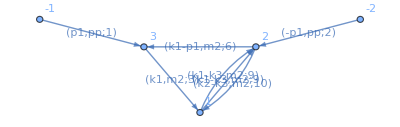

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^ν[6]) /. eps-> 0] /. s-> pp ;
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.03846

```mathematica
toint=baik Pi^3 /(x5) /. {x1 -> 0 , x2 -> 0, x3 -> 0, x4 -> 0}//FullSimplify//PowerExpand;
```

```mathematica
toint
```

-1/(x5 √(-pp^2-x5^2+2 pp (2+x5)) √(-4+x6) √x6 √(-(x5-x6)^2+4 x6))

```mathematica
(* the max cut of this graph contains the banana structure and an extra pole. Localizing on the pole, you get the max cut leading singularity. *)
maxcutBananatmp=K3Banana /. {x5 -> X6, x6 ->x5} /. X6 ->x6 //PowerExpand// FullSimplify//PowerExpand
integrand=toint /. x5 -> x5 -1//PowerExpand//FullSimplify//PowerExpand
```

x1/(√(pp^2+(-1+x5)^2-2 pp (1+x5)) √(-4+x6) √x6 √(x5^2+(-1+x6)^2-2 x5 (1+x6)))

-1/((-1+x5) √(-pp^2-(-1+x5)^2+2 pp (1+x5)) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))

```mathematica
(* the residue in x5 around 1*)
```

```mathematica
Integrate[PowerExpand[integrand (x5 - 1) /. x5 -> 1 ]//FullSimplify//PowerExpand,x6];
Coefficient[%,Log[x6]]
```

-1/(4 √(-4+pp) √pp)

```mathematica
(*
What are the other integrals?  They are not dlog forms and they are telling us about subpotologies. (in fact max cut is x5 -> 0 )
*)
```

```mathematica
(* Expand in pp to select the holomorphic solution *)
```

```mathematica
periodBanana=ω0[ρ]/.Import["./periods/k3_banana_3l/periods_0.m"][[1]];
```

```mathematica
toexpand =integrand (-I)16 √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2)(-1+x5) /. 1/Sqrt[a_]:> 1/Sqrt[-a]//FullSimplify//PowerExpand
seriestmp=  Collect[Collect[(Series[toexpand , {pp,0,25}]//Normal // PowerExpand) , {pp},Simplify]/(-1+x5), {pp}] ;
```

(16 ⅈ)/(√(pp^2+(-1+x5)^2-2 pp (1+x5)))

```mathematica
(*tmps1=Collect[(Series[-1/2Log[4 x6-(1-x5+x6)^2]+1/2Log[-((-4+x6) x6)], {x5,1,120}]//Normal)/.x5 -> x5m1 +1, {x5m1},Simplify];*)
```

```mathematica
(*E^(tmps1)/Sqrt[4-x6]/Sqrt[x6] /. {x5m1 -> 0.01, x6 ->1/2}
toexpandAgain=E^(tmps1);
tocheck=Normal[Series[toexpandAgain, {x5m1,0,50}]]/Sqrt[4-x6]/Sqrt[x6];*)
(*N[tocheck/. {x5m1 -> 10^-20, x6 ->1/2},40]
N[expandRoot /.x5 -> x5m1 +1/. {x5m1 -> 10^-20, x6 ->1/2},40]
N[1/√(4 x6-(1-x5+x6)^2) /. {x5 ->x5m1 +1}/. {x5m1 -> 10^-20, x6 ->1/2},40]*)
```

```mathematica
(*Export["./expandroots/expandroots.m",tocheck];*)
expandRoot= Import["./expandroots/expandroots.m"];
```

```mathematica
Print["done"]
(*Series and max cut do not commute *)
tmp=Residue[Series[ I seriestmp/√(4 x6-(1-x5+x6)^2)/. 1/√(4 x6-(1-x5+x6)^2) -> expandRoot /. x5m1 ->x5-1  , {x5,1,-1}],{x5,1}]//PowerExpand//Simplify;
function=(Residue[Series[tmp/√(4-x6)/Sqrt[x6],{x6,0,-1}, Assumptions->{x6 >0}]//Normal, {x6,0}]//Expand) /. pp ->ρ;
```

done

```mathematica
function=Expand[function F2[]]/. ρ^a_ F2[]:> F2[g[s,a]] /. ρ F2[] -> F2[g[ρ,1]] /. s -> ρ  /. F2[]-> F2[g[ρ,0]];
```

```mathematica
function/.extractPolySol /. ρ^a_ /; a> 5 -> 0
Series[--I/(4  √(-4+pp) √pp), {pp,0,5}, Assumptions->{Im[pp]>0}]//Normal
```

1+ρ/4+(61 ρ^2)/1024+(29 ρ^3)/2048+(14179 ρ^4)/4194304+(6803 ρ^5)/8388608

1/(8 √pp)+(√pp)/64+(3 pp^(3/2))/1024+(5 pp^(5/2))/8192+(35 pp^(7/2))/262144+(63 pp^(9/2))/2097152

```mathematica
periodBanana=Expand[periodBanana F2[]]/. ρ^a_ F2[]:> F2[g[s,a]] /. ρ F2[] -> F2[g[ρ,1]] /. s -> ρ  /. F2[]-> F2[g[ρ,0]];
```

```mathematica
combineOperator = { F1[a___]F2[b___] :> F[a,b], F1[a__]-> F[a] , F2[a__] -> F[a] };
(* move the θ operator to the right for polynomial and logs *)
moveRightPoly = {F[a___,θ, g[ρ,m_],b___]->  m F[a,g[ρ,m],b]  + F[a,g[ρ,m], θ,b]};
moveRightLog = {F[a___,θ, g[log,1],b___]->  F[a,b]  + F[a,g[log,1], θ,b],F[a___,θ, g[log,2],b___]  -> 2  F[a,g[log,1],b]  + F[a,g[log,2], θ,b]};
(* extract from the functions the logs and the polynomial *)
extractPoly = { F[g[ρ,m_],b___] -> ρ^m F[b], F[g[log,1],g[ρ,m_],b___] -> ρ^m log F[b], F[g[log,2],g[ρ,m_],b___] -> ρ^m log^2 F[b]  };
extractPolySol = { F2[g[ρ,m_]] -> ρ^m , F2[g[log,n_],g[ρ,m_]] -> ρ^m L^n };
(* Once the operator is completely to the right, it annihilates nothing *)
zeroOP = {F[θ]->0,F[θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ,θ]->0,F[θ,θ,θ,θ,θ]->0};
```

```mathematica
(* second derivative of period not needed *)
maxorder=2
ansatzDer=Sum[a[i] ρ^i F1[], {i,1,maxorder}] + Sum[b[i]F1[θ] ρ^i, {i,1,maxorder}] ;
inhomog=   Sum[c[i]ρ^i , {i,1,maxorder}]F1[] periodBanana+  Sum[d[i]ρ^i , {i,1,maxorder}]F1[](Expand[D[periodBanana /. extractPolySol,ρ] F2[]]/. ρ^a_ F2[]:> F2[g[s,a]] /. ρ F2[] -> F2[g[ρ,1]] /. s -> ρ /. F2[]  -> F2[g[ρ,0]])//Expand;
```

2

```mathematica
(ansatzDer function +inhomog // Expand) /. combineOperator /.moveRightPoly/.extractPoly /. zeroOP /. F[]-> 1 /. ρ -> ρ// PowerExpand;
```

```mathematica
sol=Equal[CoefficientList[(ansatzDer function +inhomog // Expand) /. combineOperator /.moveRightPoly/.extractPoly /. zeroOP /. F[]-> 1 /. ρ -> ρ// PowerExpand,ρ,15],0]//Solve//Flatten
```

{a[2]→-a[1]/2,b[1]→2 a[1],b[2]→-a[1]/2,c[1]→-a[1],c[2]→0,d[1]→0,d[2]→-3 a[1]}

```mathematica
ansatzDersol=ansatzDer /. sol  /. F1[]-> 1 /. a[1]-> 1
inhomogSol=Sum[c[i]ρ^i , {i,1,maxorder}] ω0+  Sum[d[i]ρ^i , {i,1,maxorder}] dω0/. sol  /. F1[]-> 1 /. a[1]-> 1
```

ρ-ρ^2/2+2 ρ F1[θ]-1/2 ρ^2 F1[θ]

-3 dω0 ρ^2-ρ ω0

```mathematica
(* the differential equation is *)
(*Solve[ρ F-ρ^2/2 F+2 ρ ρ derF-1/2 ρ^2 ρ derF  +-3 dω0 ρ^2-ρ ω0 == 0,derF]*)
(* 
derF->(2 F-6 dω0 ρ-F ρ-2 ω0)/((-4+ρ) ρ)
*)
```

```mathematica
(*the canonical candidate is given by 

(-2+d) √(-((-4+ρ) ρ)) INT[topoB,1,1,0,1,0,0,1,1,0]+1/2 (-2+d) INT[topoB,0,1,0,1,0,0,1,1,0] ((3 √ρ)/(√(4-ρ))-G3[ρ]/ω0[ρ])

*)
```

```mathematica
(* Normalize by leading singularity on max cut, it remove the F *)
```

```mathematica
(*
integrating the homogeneous part, is equivalent to integrating 
E^(-Integrate[Coefficient[(2 F-6 dω0 ρ-F ρ-2 ω0)/((-4+ρ) ρ),F],ρ])*)
```

```mathematica
Collect[D[√((4-ρ) ρ) F[ρ]-(6 ω0[ρ] ρ)/(√(-((-4+ρ) ρ))),ρ] /.F'[ρ]-> (2 F[ρ]-6 dω0 ρ-F[ρ] ρ-2 ω0)/((-4+ρ) ρ)  /. F[ρ] -> F[ρ]/√((4-ρ) ρ)/. {ω0[ρ] -> ω0, ω0'[ρ] -> dω0}, {_F,ω0,dω0},Simplify]
```

-(2 ρ (2+ρ) ω0)/(-((-4+ρ) ρ))^(3/2)

```mathematica
G3'[ρ]->((2+ρ) ω0[ρ])/((4-ρ)^(3/2) √ρ)
(* so the correction can be obtained by removing F/omega0 banana, I need something that gives me a non trivial thing along that contour (the one that gives me the holomorphic solution ) *)
```

G3'[ρ]→((2+ρ) ω0[ρ])/((4-ρ)^(3/2) √ρ)

## 3 loop Triangle sunrise dlog (G operator derived) pp -> inf

```mathematica
K3Banana=x1/(√(-4+x5) √x5 √(pp^2+(-1+x6)^2-2 pp (1+x6)) √(x5^2+(-1+x6)^2-2 x5 (1+x6)));
```

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^ν[6]) /. eps-> 0] /. s-> pp ;
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.089771

```mathematica
toint=baik Pi^3 /(x5) /. {x1 -> 0 , x2 -> 0, x3 -> 0, x4 -> 0}//FullSimplify//PowerExpand;
integrand=toint /. x5 -> x5 -1//PowerExpand//FullSimplify//PowerExpand
(* the residue in x5 around 1*)
Integrate[PowerExpand[integrand (x5 - 1) /. x5 -> 1 ]//FullSimplify//PowerExpand,x6];
Coefficient[%,Log[x6]]  /. pp -> 1/z // FullSimplify
```

-1/((-1+x5) √(-pp^2-(-1+x5)^2+2 pp (1+x5)) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))

-z/(4 √(1-4 z))

```mathematica
Series[z/(√(1-4 z)), {z,0,3}]
```

z+2 z^2+6 z^3+O[z]^4

```mathematica
(*
What are the other integrals?  They are not dlog forms and they are telling us about subpotologies. (in fact max cut is x5 -> 0 )
*)
```

```mathematica
(* Expand in pp to select the holomorphic solution *)
```

```mathematica
periodBanana=ω0[ρ]/.Import["./periods/k3_banana_3l/periodsInf.m"][[1]];
```

```mathematica
toint=baik Pi^3 /(x5) /. {x1 -> 0 , x2 -> 0, x3 -> 0, x4 -> 0}//FullSimplify//PowerExpand;
integrand = toint;
```

```mathematica
integrand=integrand /. pp -> 1/z /. 1/Sqrt[a_] :> 1/Sqrt[Factor[a]]//PowerExpand//FullSimplify;
toexpand =integrand /. 1/Sqrt[a_]:> 1/Sqrt[-a]//FullSimplify//PowerExpand
```

z/(x5 √((x5-x6)^2-4 x6) √(4-x6) √x6 √(-1+z (4+x5 (2-x5 z))))

```mathematica
(*max cut*)
series=(Series[toexpand , {z,0,15},Assumptions->Im[(4+2 x5) z-x5^2 z^2]≥0]//Normal // PowerExpand) ;
series2 =Residue[ Series[series,{x5,0,-1}]//Normal // PowerExpand, {x5,0}];
series3=Series[(series2 )/. 1/Sqrt[a_] :> 1/Sqrt[Factor[a]]//PowerExpand, {x6,0,-1}, Assumptions->Im[x6]≥0]//Normal;
functionToGuess=Residue[series3 (-4),{x6,0}]
```

z+2 z^2+6 z^3+20 z^4+70 z^5+252 z^6+924 z^7+3432 z^8+12870 z^9+48620 z^10+184756 z^11+705432 z^12+2704156 z^13+10400600 z^14+40116600 z^15

```mathematica
(*max cut*)
series=(Series[toexpand , {z,0,15},Assumptions->Im[(4+2 x5) z-x5^2 z^2]≥0]//Normal // PowerExpand) ;
series2 =Residue[ Series[(series /. x5 ->1/x5)/x5/x5,{x5,0,-1}]//Normal // PowerExpand, {x5,0}];
series3=Series[(series2  /. x6 -> 1/x6)/x6/x6/. 1/Sqrt[a_] :> 1/Sqrt[Factor[a]]//PowerExpand, {x6,0,-1}, Assumptions->Im[x6]≥0]//Normal;
functionToGuess=Residue[-series3 ,{x6,0}];
```

```mathematica
function=Expand[(functionToGuess /. z ->ρ )  F2[]] /. F2[]ρ^n_ :>  F2[g[ρ,n]]
```

F2[g[ρ,2]]+8 F2[g[ρ,3]]+64 F2[g[ρ,4]]+576 F2[g[ρ,5]]+5876 F2[g[ρ,6]]+66176 F2[g[ρ,7]]+798848 F2[g[ρ,8]]+10113536 F2[g[ρ,9]]+132410764 F2[g[ρ,10]]+1777039008 F2[g[ρ,11]]+24307857344 F2[g[ρ,12]]+337590162432 F2[g[ρ,13]]+4747089191872 F2[g[ρ,14]]+67448190921728 F2[g[ρ,15]]

```mathematica
periodBanana = Import["./periods/k3_banana_3l/periodsInf.m"][[1,2]];
```

```mathematica
Collect[ρ-1/2-2ρ θ+1/2  θ /. ρ ->z, {θ,z},Simplify]
Collect[-3 ρ^2 π0 +ρ π0 /. ρ ->z, {θ,z},Simplify]
```

-1/2+z+(1/2-2 z) θ

z π0-3 z^2 π0

```mathematica
op1=ρ-1/2-2ρ F1[θ]+1/2  F1[θ]
inhomg=-3 ρ^2 dω0 +ρ ω0
```

-1/2+ρ+F1[θ]/2-2 ρ F1[θ]

-3 dω0 ρ^2+ρ ω0

```mathematica
Expand[op1 G ]+ inhomog
```

-G/2+G ρ-3 dω0 ρ^2+ρ ω0+1/2 G F1[θ]-2 G ρ F1[θ]

```mathematica
(4 op1 function  // Expand)/.combineOperator //. moveRightPoly //. extractPoly /. zeroOP /. F[]-> 1 
(-3 ρ^2 D[periodBanana ,ρ]+ρ periodBanana //Expand) /. ρ^n_ /; n> 12 -> 0
%%+%
```

2 ρ^2+20 ρ^3+224 ρ^4+2816 ρ^5+38024 ρ^6+535568 ρ^7+7742720 ρ^8+113885696 ρ^9+1695673304 ρ^10+25477562096 ρ^11+385501584896 ρ^12+5865841022720 ρ^13+89665302745472 ρ^14+1375863713086208 ρ^15-7823990146920448 ρ^16

-2 ρ^2-20 ρ^3-224 ρ^4-2816 ρ^5-38024 ρ^6-535568 ρ^7-7742720 ρ^8-113885696 ρ^9-1695673304 ρ^10-25477562096 ρ^11-385501584896 ρ^12

5865841022720 ρ^13+89665302745472 ρ^14+1375863713086208 ρ^15-7823990146920448 ρ^16

```mathematica
combineOperator = { F1[a___]F2[b___] :> F[a,b], F1[a__]-> F[a] , F2[a__] -> F[a] };
(* move the θ operator to the right for polynomial and logs *)
moveRightPoly = {F[a___,θ, g[ρ,m_],b___]->  m F[a,g[ρ,m],b]  + F[a,g[ρ,m], θ,b]};
moveRightLog = {F[a___,θ, g[log,1],b___]->  F[a,b]  + F[a,g[log,1], θ,b],F[a___,θ, g[log,2],b___]  -> 2  F[a,g[log,1],b]  + F[a,g[log,2], θ,b]};
(* extract from the functions the logs and the polynomial *)
extractPoly = { F[g[ρ,m_],b___] -> ρ^m F[b], F[g[log,1],g[ρ,m_],b___] -> ρ^m log F[b], F[g[log,2],g[ρ,m_],b___] -> ρ^m log^2 F[b]  };
extractPolySol = { F2[g[ρ,m_]] -> ρ^m , F2[g[log,n_],g[ρ,m_]] -> ρ^m L^n };
(* Once the operator is completely to the right, it annihilates nothing *)
zeroOP = {F[θ]->0,F[θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ,θ]->0,F[θ,θ,θ,θ,θ]->0};
```

```mathematica
op1=(ρ-1/2-2ρ F1[θ]+1/2  F1[θ])
inhomog=-3 ρ^2 dω0 +ρ ω0
```

-1/2+ρ+F1[θ]/2-2 ρ F1[θ]

-3 dω0 ρ^2+ρ ω0

```mathematica
operator=Collect[(ρ G[ρ]-1/2 G[ρ]-2ρ ρ D[G[ρ],ρ]+1/2  ρ  D[G[ρ],ρ])   +-3 ρ^2 D[π0[ρ],ρ] +ρ π0[ρ], {_π0, _G},Simplify]
```

(-1/2+ρ) G[ρ]+ρ π0[ρ]-1/2 ρ ((-1+4 ρ) G'[ρ]+6 ρ π0'[ρ])

```mathematica
Solve[(-1/2+ρ) G[ρ]+ρ π0[ρ]-1/2 ρ ((-1+4 ρ) G'[ρ]+6 ρ π0'[ρ]) == 0, G'[ρ]]
```

{{G'[ρ]→(-G[ρ]+2 ρ G[ρ]+2 ρ π0[ρ]-6 ρ^2 π0'[ρ])/(ρ (-1+4 ρ))}}

```mathematica
leadingsing=DSolve[(-1/2+ρ) G[ρ]-1/2 ρ ((-1+4 ρ) G'[ρ])== 0,G[ρ],ρ]/.C[1]-> 1//Flatten
```

{G[ρ]→ρ/(√(1-4 ρ))}

```mathematica
D[1/(ρ/(√(1-4 ρ)))G[ρ],ρ]   /.G'[ρ]->(-G[ρ]+2 ρ G[ρ]+2 ρ π0[ρ]-6 ρ^2 π0'[ρ])/(ρ (-1+4 ρ))/.   G[ρ] -> nG[ρ]/(ρ/(√(1-4 ρ))) //Simplify
Collect[D[G[ρ],ρ]  -(-(2 (π0[ρ]-3 ρ π0'[ρ]))/(√(1-4 ρ) ρ)), {_G, _π0}, Simplify]
```

-(2 (π0[ρ]-3 ρ π0'[ρ]))/(√(1-4 ρ) ρ)

(2 π0[ρ])/(√(1-4 ρ) ρ)+G'[ρ]-(6 π0'[ρ])/(√(1-4 ρ))

```mathematica
Solve[(2 π0[ρ])/(√(1-4 ρ) ρ)+G'[ρ]-(6 π0'[ρ])/(√(1-4 ρ)) == 0,G'[ρ]]
```

{{G'[ρ]→(2 (-π0[ρ]+3 ρ π0'[ρ]))/(√(1-4 ρ) ρ)}}

```mathematica
Collect[D[G[ρ] -  (6  π0[ρ])/(1-4 ρ)^(1/2),ρ]  /. {G'[ρ]->(2 (-π0[ρ]+3 ρ π0'[ρ]))/(√(1-4 ρ) ρ)} /.  G[ρ] -> G[ρ] +  (6 ρ^2 π0[ρ])/(1-4 ρ)^(3/2),  {_G, _π0}, Simplify]
```

```mathematica
-((2+4 ρ) π0[ρ])/((1-4 ρ)^(3/2) ρ)//Factor
```

-(2 (1+2 ρ) π0[ρ])/((1-4 ρ)^(3/2) ρ)

```mathematica
(*Gfinal = (√(1-4 ρ))/ρ Gstart - (6  π0[ρ])/(1-4 ρ)^(1/2)*)
(* D[Gfinal[ρ],ρ]  = -((2+4 ρ) π0[ρ])/((1-4 ρ)^(3/2) ρ) *)
```

## 3 loop triangle bubble - bubble (G derived) corner top (written and checked with diff eq)

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik (32 π^(5/2) Gamma[1/2 (1-2 eps)] Gamma[-eps]^2) /((x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^ν[6] x7^ν[7] x8^ν[8] d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6]⋀d[x7]⋀d[x8]))/. eps-> 0] /. s-> pp ;
baik= baik// FullSimplify
```

{{{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

Drop::drop: Cannot drop positions 1 through 1 in {}.

Solve::svars: Equations may not give solutions for all "solve" variables.

{-Graphics-,-Graphics-}

"Total runtime= "  0.112044

-((8 ⅈ √(3-pp^2-x1^2+4 x4-4 x6+2 x7+2 x1 (1+2 x4-2 x6+x7-2 x8)-4 x8-(-2 x6+x7+2 x8)^2+2 pp (1+x1-2 x6+x7+2 x8)))/((pp^2 (1+x4)+(1+x4) (1+x1-x7)^2+4 x6 (1+x1-x7) x8+4 x7 x8^2-2 pp (1+x1+x4+x1 x4+x7+x4 x7+2 x6 (-x6+x8))) (-2-x2+x2^2+pp^2 (1+x2)-x3-x2 x3+x3^2+x1^2 (1+x3)-2 x4-x2 x4+x2^2 x4-2 x3 x4+x4^2-x5-x2 x5-x3 x5-x4 x5-2 x2 x4 x5+x5^2+x4 x5^2+2 x6+2 x2 x6+2 x3 x6-2 x2 x3 x6-2 x4 x6+2 x2 x4 x6+2 x2 x5 x6+2 x3 x5 x6-2 x4 x5 x6-2 x5^2 x6+4 x6^2+4 x5 x6^2-x7-x2 x7-x3 x7+x2 x3 x7+x4 x7-x2 x4 x7-x2 x5 x7-x3 x5 x7+x4 x5 x7+x5^2 x7-4 x6 x7-4 x5 x6 x7+x7^2+x5 x7^2-x1 (1-x3^2+2 x4+x2 (1+x3+x4-x5)+x5-2 x6+x7-(x4-x5) (x4-2 x6+x7)+x3 (2 x4+x5-2 x6+x7))+2 x1 (1+x2+x3-x4+2 x6-x7) x8+2 (1-x2^2+x3-x4+x5-2 x6+x7+x5 (-x3+x4-2 x6+x7)+x2 (x3-x4+x5-2 x6+x7)) x8+4 (1+x2) x8^2-pp (1-x2^2+x3-x4+x5-2 x6+x1 (1+x2+x3-x4+2 x6-x7)+x7+x5 (-x3+x4-2 x6+x7)+4 x8+x2 (x3-x4+x5-2 x6+x7+4 x8)))))

```mathematica
(* First two loops, two loop sunrise, loop momenta k3, k4 *)
(*  P1 = p1+k1 
(k3)^2-m2, , (k3 + P1)^2-m2
*)
propfirstloop={sp[k3,k3]-m2,
sp[k3,k3] + pp + k1k1 + 2 k1p1 +2 sp[k3,P1]-m2}
(**)
sps= Union@Cases[propfirstloop,_sp,∞];
(*physical props are x1, x2, x3*)
isptoprop=Solve[Thread[Equal[propfirstloop , {x1,x2}]],sps]//Flatten;
```

{-m2+sp[k3,k3],k1k1+2 k1p1-m2+pp+sp[k3,k3]+2 sp[k3,P1]}

```mathematica
SetAttributes[sp,Orderless]
```

```mathematica
external = {P1};
allmomenta = {P1,k3};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,2}, {j,1,2}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=%/. sp[P1,P1]-> pp + k1k1 + 2 k1p1/. isptoprop//Simplify;
baik=detInternalMomenta^((d-1-1-1)/2); (* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,1}, {j,1,1}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det ;
mat2 =mat2/. sp[P1,P1]-> pp + k1k1 + 2 k1p1;
detExternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop ;
baik=baik  detExternalMomenta^((2-d)/2) ;(* (1+E-d)/2 , E independent external momenta *)
firstLoopBaik = baik;
```

```mathematica
firstLoopBaik/. d->5//Variables
```

{k1k1,k1p1,m2,pp,x1,x2}

```mathematica
propsecondloop={sp[k1,k1]-m2,
sp[k1,k1] +2 sp[k1,k2] + k2k2-m2,
(* unphysical one *) pp +2 sp[p1,k1]+ sp[k1,k1]}
(*physical prop are 5 and 6*)
isptoprop=Thread[Equal[propsecondloop , {x3,x4,x40}]]//Solve//Flatten
external = {k2,p1};
allmomenta = {p1,k1,k2};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,3}, {j,1,3}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop;
(*physical prop are 5 and 6*)
baik2=detInternalMomenta^((d-1-2-1)/2);(* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,2}, {j,1,2}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det 
detExternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop 
baik2=baik2  detExternalMomenta^((1+2-d)/2);(* (1+E-d)/2 ,E independent external momenta *)
```

{-m2+sp[k1,k1],k2k2-m2+sp[k1,k1]+2 sp[k1,k2],pp+sp[k1,k1]+2 sp[k1,p1]}

{sp[k1,k1]→m2+x3,sp[k1,k2]→-k2k2/2-x3/2+x4/2,sp[k1,p1]→-m2/2-pp/2-x3/2+x40/2}

-sp[k2,p1]^2+sp[k2,k2] sp[p1,p1]

-k2p1^2+k2k2 pp

```mathematica
Solve[sp[k1,k1]==m2+x3,x3]
```

{{x3→-m2+sp[k1,k1]}}

```mathematica
firstLoopBaik =firstLoopBaik/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]}/.isptoprop;
secondLoopBaik =baik2/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]};
secondLoopBaik/.d-> 20//Variables
```

{k2k2,k2p1,m2,pp,x3,x4,x40}

```mathematica
(*
k2^2, and isp k2.p1, bubble kinematics
*)
propthirdloop={sp[k2,k2]-m2,sp[k2,p1]}
isptoprop=Thread[Equal[propthirdloop , {x5,x41}]]//Solve//Flatten
external = {p1};
allmomenta = {p1,k2};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,2}, {j,1,2}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=% /. sp[p1,p1]-> pp/. isptoprop;
baik2=detInternalMomenta^((d-1-1-1)/2);(* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,1}, {j,1,1}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det 
detExternalMomenta=% /. sp[p1,p1]-> pp /. isptoprop 
baik2=baik2  detExternalMomenta^((1+1-d)/2);(* (1+E-d)/2 ,E independent external momenta *)
thirdLoopBaik = baik2;
```

{-m2+sp[k2,k2],sp[k2,p1]}

{sp[k2,k2]→m2+x5,sp[k2,p1]→x41}

sp[p1,p1]

pp

```mathematica
firstLoopBaik =firstLoopBaik/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]};
secondLoopBaik  = secondLoopBaik/. {k2k2 -> sp[k2,k2], k2p1-> sp[k2,p1]}/.isptoprop;
(*physical props are x1, x2, x3, x4,x5,x6*)
baik = firstLoopBaik secondLoopBaik thirdLoopBaik /. {x40-> x7,x41->x8,x42->x9,x43->x10} /. m2->1;
Variables[baik/. d-> 2]
```

{pp,x1,x2,x3,x4,x5,x7,x8}

```mathematica
baikd2=firstLoopBaik secondLoopBaik thirdLoopBaik /. d->2 /. m2-> 1//FullSimplify
```

-(8/(√(-(x1-x2)^2+2 (2+x1+x2) x40-x40^2) (1-2 x40+x40^2-2 x41+2 x4 x41+2 x40 x41-2 x4 x40 x41+4 x41^2+(-1+x40) (-1+x40+2 x41) x5+pp^2 (1+x5)+x3^2 (1-2 x41+x5)+2 x3 (1+x40 (-1+x41-x5)+x41 (-2+x4+2 x41-x5)+x5)+pp (-1+x3^2-2 x40-2 x41-2 x3 (x4+x41)+x4 (-2+x4+2 x41)-2 (x4+x40+x41) x5+x5^2))))

```mathematica
maxcut = baikd2 /. {x1->0,x2-> 0,x3->0,x4->0,x5->0}//FullSimplify;
```

```mathematica
maxcut  /. x40  -> y /. x41 -> w /. pp -> 1/z  // Together//FullSimplify
```

-(8 z^2)/(√(-((-4+y) y)) (1+z (-1-2 w-2 y+(4 w^2+2 w (-1+y)+(-1+y)^2) z)))

```mathematica
int1=Integrate[maxcut,x41]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint2=Coefficient[int1, logs][[1]];
toint=toint2 // PowerExpand
```

-4/(√3 √(-4+x40) √x40 √(pp^2+(-1+x40)^2-2 pp (1+x40)))

```mathematica
-4/(√3 √(-4+x40) √x40 √(pp^2+(-1+x40)^2-2 pp (1+x40)))/. x40 -> x6 ;
```

```mathematica
(*MAX CUT, sunrise 2 loop, elliptic *)
baik =baikd2 /. {x40 -> x6, x41 -> x7};
toint=baik/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0}//FullSimplify;
int1=Integrate[toint,x7]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint2=Coefficient[int1, logs][[1]];
toint=toint2 // PowerExpand;
(Series[toint /. pp -> pp, {pp,0,5}]//Normal//PowerExpand)
Residue[Normal[Series[% 3 /4 I, {x6,1,-1},Assumptions->Im[x6]<0]],{x6,1}]//Expand
Import["./periods/elliptic_sunrise_2l/periods.m"][[1,2]]/.ρ^n_ /; n> 5 ->0
```

-4/(√3 √(-4+x6) (-1+x6) √x6)-(4 pp (1+x6))/(√3 √(-4+x6) (-1+x6)^3 √x6)-(4 pp^2 (1+4 x6+x6^2))/(√3 √(-4+x6) (-1+x6)^5 √x6)-(4 pp^3 (1+x6) (1+8 x6+x6^2))/(√3 √(-4+x6) (-1+x6)^7 √x6)-(4 pp^4 (1+16 x6+36 x6^2+16 x6^3+x6^4))/(√3 √(-4+x6) (-1+x6)^9 √x6)-(4 pp^5 (1+x6) (1+24 x6+76 x6^2+24 x6^3+x6^4))/(√3 √(-4+x6) (-1+x6)^11 √x6)

1+pp/3+(5 pp^2)/27+(31 pp^3)/243+(71 pp^4)/729+(517 pp^5)/6561

1+ρ/3+(5 ρ^2)/27+(31 ρ^3)/243+(71 ρ^4)/729+(517 ρ^5)/6561

```mathematica
(*MAX CUT, taking x6 -> 1/x6, it cannot change *)
baik =baikd2 /. {x40 -> x6, x41 -> x7};
toint=baik/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0}//FullSimplify;
int1=Integrate[toint,x7]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint2=Coefficient[int1, logs][[1]];
toint=toint2 // PowerExpand;
(Series[toint /. pp -> pp, {pp,0,5}]//Normal//PowerExpand) ;
Residue[Series[Collect[(%  3 /4 I/. x6 -> 1/x6)/x6/x6, {pp}, FullSimplify], {x6,1,-1},Assumptions->Im[x6]≤0]//Normal, {x6,1}]//Expand
```

1+pp/3+(5 pp^2)/27+(31 pp^3)/243+(71 pp^4)/729+(517 pp^5)/6561

```mathematica
(*MAX CUT at inf,  sunrise 2 loop, elliptic *)
baik =baikd2 /. {x40 -> x6, x41 -> x7};
toint=baik/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0}//FullSimplify;
int1=Integrate[toint,x7]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint2=Coefficient[int1, logs][[1]];
toint=toint2 // PowerExpand;
Collect[(Series[toint /. pp -> 1/s, {s,0,5}]//Normal//PowerExpand)//Together//Simplify, {s}]
(% /. x6 -> 1/x6)/x6/x6//FullSimplify;
Residue[Normal[Series[-% Sqrt[3] /4 , {x6,0,-1},Assumptions->Im[x6]<0]],{x6,0}]//Expand
```

-(4 s)/(√3 √(-4+x6) √x6)-(4 s^2 (1+x6))/(√3 √(-4+x6) √x6)-(4 s^3 (1+4 x6+x6^2))/(√3 √(-4+x6) √x6)-(4 s^4 (1+9 x6+9 x6^2+x6^3))/(√3 √(-4+x6) √x6)-(4 s^5 (1+16 x6+36 x6^2+16 x6^3+x6^4))/(√3 √(-4+x6) √x6)

s+3 s^2+15 s^3+93 s^4+639 s^5

```mathematica
(*Expand around MUM point for the subcut, this is a K3*)
baik =baikd2 /. {x40 -> x6, x41 -> x7};
toint=baik/x3/. {x1-> 0,x2-> 0,x4-> 0,x5-> 0}//FullSimplify;
int1=Integrate[toint,x7]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint=Coefficient[int1, logs][[1]]
```

4/(√(-3+x3) x3 √(1+x3) √(-((-4+x6) x6)) √(pp^2+(1+x3-x6)^2-2 pp (1+x3+x6)))

```mathematica
(* max cut*)
toint2=toint /. pp ->1/z /. 1/Sqrt[a_] :>  1/Sqrt[Factor[a]] // PowerExpand;
tmp=Series[toint2, {z,0,5}]//Normal//Together
tmp=Residue[Series[(tmp /. x6 ->1/x6)/x6/x6, {x6,0,-1}]//Normal, {x6,0}]
Residue[Normal[Series[-tmp Sqrt[3]/4, {x3,0,-1},Assumptions->Im[x3]>0]], {x3,0}]//Expand
```

-1/(√(-3+x3) x3 √(1+x3) √(-4+x6) √x6)4 ⅈ (z+z^2+x3 z^2+x6 z^2+z^3+2 x3 z^3+x3^2 z^3+4 x6 z^3+4 x3 x6 z^3+x6^2 z^3+z^4+3 x3 z^4+3 x3^2 z^4+x3^3 z^4+9 x6 z^4+18 x3 x6 z^4+9 x3^2 x6 z^4+9 x6^2 z^4+9 x3 x6^2 z^4+x6^3 z^4+z^5+4 x3 z^5+6 x3^2 z^5+4 x3^3 z^5+x3^4 z^5+16 x6 z^5+48 x3 x6 z^5+48 x3^2 x6 z^5+16 x3^3 x6 z^5+36 x6^2 z^5+72 x3 x6^2 z^5+36 x3^2 x6^2 z^5+16 x6^3 z^5+16 x3 x6^3 z^5+x6^4 z^5)

-(4 ⅈ (z+3 z^2+x3 z^2+15 z^3+10 x3 z^3+x3^2 z^3+93 z^4+93 x3 z^4+21 x3^2 z^4+x3^3 z^4+639 z^5+852 x3 z^5+318 x3^2 z^5+36 x3^3 z^5+x3^4 z^5))/(√(-3+x3) x3 √(1+x3))

z+3 z^2+15 z^3+93 z^4+639 z^5

```mathematica
(* second solution*)
Residue[Normal[Series[((I)tmp /4 /. x3 ->1/x3)/x3/x3, {x3,0,-1},Assumptions->Im[x3]>0]], {x3,0}]//Expand
```

z^2+11 z^3+117 z^4+1285 z^5

```mathematica
(*Expand around MUM point for the subcut, banana K3*)
baik =baikd2 /. {x40 -> x6, x41 -> x7};
toint=baik/. {x1-> 0,x2-> 0,x4-> 0,x5-> 0}//FullSimplify;
int1=Integrate[toint,x7]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint=Coefficient[int1, logs][[1]];
toint2=toint /. pp ->1/z /. 1/Sqrt[a_] :>  1/Sqrt[Factor[a]] // PowerExpand;
tmp=Series[toint2, {z,0,5}]//Normal//Together;
tmp=Residue[Series[(tmp /. x6 ->1/x6)/x6/x6, {x6,0,-1}]//Normal, {x6,0}]
Residue[Normal[Series[(I tmp /4 /. x3 -> 1/x3)/x3/x3, {x3,0,-1},Assumptions->Im[x3]>0]], {x3,0}]//Expand
```

-(4 ⅈ (z+3 z^2+x3 z^2+15 z^3+10 x3 z^3+x3^2 z^3+93 z^4+93 x3 z^4+21 x3^2 z^4+x3^3 z^4+639 z^5+852 x3 z^5+318 x3^2 z^5+36 x3^3 z^5+x3^4 z^5))/(√(-3+x3) √(1+x3))

z+4 z^2+28 z^3+256 z^4+2716 z^5

### Differential Operator at z -> ∞

```mathematica
(*Expand around MUM point for the subcut, this is a K3*)
baik =baikd2 /. {x40 -> x6, x41 -> x7};
toint=baik/x3/. {x1-> 0,x2-> 0,x4-> 0,x5-> 0}//FullSimplify;
int1=Integrate[toint,x7]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint=Coefficient[int1, logs][[1]];
toint2=toint /. pp ->1/s /. 1/Sqrt[a_] :>  1/Sqrt[Factor[a]] // PowerExpand// Simplify
```

-(4 ⅈ s)/(√(-3+x3) x3 √(1+x3) √(-4+x6) √x6 √(1+s^2 (1+x3-x6)^2-2 s (1+x3+x6)))

```mathematica
toint2 √(1+s^2 (1+x3-x6)^2-2 s (1+x3+x6))√(-4+x6) √x6
```

-(4 ⅈ s)/(√(-3+x3) x3 √(1+x3))

```mathematica
(*tmpsqrt=Collect[Series[E^(-1/2 Normal[Series[Log[1+s^2 (1+x3-x6)^2-2 s (1+x3+x6)], {s,0,60}]]), {s,0,50}]//Normal, {s}, Factor];
series=Series[((1/(√(-4+x6) √x6)/. x6 -> 1/x6)/x6/x6 // FullSimplify)(tmpsqrt/. x6 ->1/x6),{x6,0,-1}]//Normal;
num=Collect[Coefficient[series,x6,-1], {s},Simplify];*)
```

```mathematica
(*(* this is actually the max cut ...*)
function1=Residue[Series[(4 ⅈ s)/(√(-3+x3) x3 √(1+x3))num /4 Sqrt[3], {x3, 0,-1}, Assumptions->Im[x3]≥0]//Normal, {x3,0}]/.s-> z//Expand;*)
```

```mathematica
(*(* this is a new function instead.*)
function2=Residue[Series[(((4 ⅈ s)/(√(-3+x3) x3 √(1+x3))/(ⅈ √3)/. x3 -> 1/x3 )/x3/x3 // FullSimplify)(num /4 Sqrt[3] /. x3 -> 1/x3), {x3, 0,-1}, Assumptions->Im[x3]≥0]//Normal, {x3,0}]/.s-> z//Expand;*)
```

```mathematica
(*Export["./2loopHard/gfunctionExpansion_50orders.m",function2]*)
```

```mathematica
(*Import["./2loopHard/gfunctionExpansion_50orders.m"]*)
```

```mathematica
banana3loopinf = Import["./periods/k3_banana_3l/periodsInf.m"][[1,2 ]];
sunriseatinf = Import["./periods/elliptic_sunrise_2l/periods_inf.m"][[1,2 ]];
```

```mathematica
(* move in the preambule *)
generateFunctionForAnsatz[function_] := Module[{sol},
sol=Expand[(function F2[])]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
Return[sol]
]
generateAnsatzDer[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*)] :=Module[{op},
If[derorder>100, Print["Nein!"]];
f1s=F1/@Table[Table[θ, {i,1,n}], {n,0,100}]  /. F1[List[a___]]:> F1[a];
op=Sum[Sum[Subscript[a, i,j] ρ^j, {j,0,orderpoly}]f1s[[i+1]], {i,0,derorder}];
Return[op]
] 
generateAnsatzInhomog[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*), function_] :=Module[{op,functionForAnsatz},
If[derorder>10, Print["Nein!"]];
derivatives= Do[der[i] = D[function,{ρ,i}], {i,0,10}];
Do[functionForAnsatz[i] = generateFunctionForAnsatz[der[i]], {i,0,10}];
op=Sum[Sum[Subscript[b, i,j] ρ^j, {j,0,orderpoly}]F1[]functionForAnsatz[i], {i,0,derorder}];
op  =  Collect[Expand[op] //. combineOperator //.extractPoly /. zeroOP /. F[]-> 1,ρ, Simplify];
Return[op]
] 
generateAnsatzInhomogFormal[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*)] :=Module[{op,functionForAnsatz},
If[derorder>10, Print["Nein!"]];
derivatives= Do[der[i] = D[f[ρ],{ρ,i}], {i,0,10}];
Do[functionForAnsatz[i] = generateFunctionForAnsatz[der[i]], {i,0,10}];
op=Sum[Sum[Subscript[b, i,j] ρ^j, {j,0,orderpoly}]F1[]functionForAnsatz[i], {i,0,derorder}];
op  =  Collect[Expand[op] //. combineOperator //.extractPoly /. zeroOP /. F[]-> 1,ρ, Simplify];
Return[op]
]
```

```mathematica
functionToGuess = Import["./2loopHard/gfunctionExpansion_50orders.m"];
```

```mathematica
maxorderPoly = 5;
maxDerDer= 2;
maxDerInhom = 3;
derOp = generateAnsatzDer[maxorderPoly, maxDerDer];
inhomog = generateAnsatzInhomog[maxorderPoly, maxDerInhom (*max derivative omegas banana*), banana3loopinf];
inhomogFormal= generateAnsatzInhomogFormal[maxorderPoly, maxDerInhom (*max derivative omegas banana*)];
derApplied=Expand[derOp generateFunctionForAnsatz[functionToGuess/. z-> ρ]] //.combineOperator//.moveRightPoly//.moveRightLog//.zeroOP //. extractPoly//.zeroOP /. F[]-> 1;
sol=Solve[Thread[Equal[CoefficientList[Expand[derApplied + inhomog], ρ,40],0]]]//Flatten;
```

```mathematica
sol = Join[sol /. {Subscript[a, 0,0]->0, Subscript[a, 0,1]->1, Subscript[b, 0,0]-> 0}, {Subscript[a, 0,0]->0, Subscript[a, 0,1]->1, Subscript[b, 0,0]-> 0}];
```

```mathematica
Collect[derOp/.sol  /. F1[] -> 1, {_F1},Factor]
inhomogFormal /. sol //Simplify
```

-ρ (-1+3 ρ)+2 ρ (-1+5 ρ) F1[θ]+(-1+ρ) ρ (-1+9 ρ) F1[θ,θ]

1/2 ρ^2 (-f[ρ]+ρ ((-1+10 ρ) f'[ρ]+5 ρ (-1+2 ρ) f''[ρ]))

```mathematica
sunriseatinf1=Import["./periods/elliptic_sunrise_2l/periods_inf.m"][[2,2]];
sunriseatinf=Import["./periods/elliptic_sunrise_2l/periods_inf.m"][[1,2]];
(*the homogenous part is just the sunrise operator, so it should annihilates the sunrise period, in fact..*)
toapplyto=Expand[sunriseatinf F2[]] /. z -> ρ /. F2[]ρ^n_ :> F2[g[ρ,n]] /. ρ F2[] -> F2[g[ρ,1]];
((-ρ (-1+3 ρ)+2 ρ (-1+5 ρ) F1[θ]+(-1+ρ) ρ (-1+9 ρ) F1[θ,θ] )toapplyto // Expand)//.combineOperator //. moveRightPoly /.zeroOP  //.extractPoly /.zeroOP  /. ρ^n_ /; n > 150 -> 0
(*the homogenous part is just the sunrise operator, so it should annihilates the sunrise period, in fact..*)
toapplyto=Expand[sunriseatinf1] /. z -> ρ /. {Log[ρ]^m_  ρ^n_ :>  F2[g[log,m],g[ρ,n]],Log[ρ]^m_  ρ :>  F2[g[log,m],g[ρ,1]],Log[ρ]^m_ :> F2[g[log,m]],Log[ρ]ρ^n_ :> F2[g[log,1],g[ρ,n]],Log[ρ]ρ :> F2[g[log,1],g[ρ,1]],Log[ρ]->F2[g[log,1]],ρ^n_:> F2[g[ρ,n]] , ρ:> F2[g[ρ,1]]};
(((-ρ (-1+3 ρ)+2 ρ (-1+5 ρ) F1[θ]+(-1+ρ) ρ (-1+9 ρ) F1[θ,θ] )toapplyto // Expand)//.combineOperator//.moveRightLog  //. moveRightPoly  //.extractPoly //.zeroOP //Expand) /. ρ^n_ /; n > 150 -> 0 /. F[]-> 1/. ρ^n_ /; n > 10 -> 0// Simplify
```

0

0

#### simplify eqs.

```mathematica
sunriseatinf1=Import["./periods/elliptic_sunrise_2l/periods_inf.m"][[2,2]];
sunriseatinf=Import["./periods/elliptic_sunrise_2l/periods_inf.m"][[1,2]];
```

```mathematica
-((D[sunriseatinf  ,ρ](Import["./periods/elliptic_sunrise_2l/periods_inf.m"][[2,2]])- D[Import["./periods/elliptic_sunrise_2l/periods_inf.m"][[2,2]],ρ]sunriseatinf//Simplify)(1-10 ρ+9 ρ^2)/ρ//Expand) /. ρ^n_ /; n> 140 -> 0
Δ =z/(1-10 z+9 z^2)
```

1

z/(1-10 z+9 z^2)

```mathematica
der
```

der

```mathematica
Series[D[(functionToGuess / sunriseatinf /. ρ-> z),z], {z,0,2}]
```

1+16 z+234 z^2+O[z]^3

```mathematica
Series[(sunriseatinf^2 /. ρ ->z)/Δ D[(functionToGuess / sunriseatinf /. ρ-> z),z], {z,0,40}]//Normal;
D[%,z] /. z^n_ /; n> 10 -> 0
Series[sunriseatinf  (1/2 ρ^2 ( 1/((-1+ρ) ρ (-1+9 ρ)ρ^2) )(-banana3loopinf+ρ ((-1+10 ρ) D[banana3loopinf,ρ]+5 ρ (-1+2 ρ)  D[D[banana3loopinf,ρ],ρ])))/Δ/.ρ-> z, {z,0,10}]//Normal
```

1+24 z+474 z^2+8656 z^3+153180 z^4+2664768 z^5+45822322 z^6+781083552 z^7+13222712394 z^8+222595529920 z^9+3730014653442 z^10

-1-24 z-474 z^2-8656 z^3-153180 z^4-2664768 z^5-45822322 z^6-781083552 z^7-13222712394 z^8-222595529920 z^9-3730014653442 z^10

```mathematica
(1/2 ρ^2 (-ban+ρ ((-1+10 ρ) banp+5 ρ (-1+2 ρ)  banpp)))
```

1/2 ρ^2 (-ban+ρ (5 banpp ρ (-1+2 ρ)+banp (-1+10 ρ)))

```mathematica
(*(* Split the matrix {{ω0,ω1},{dω0,dω1}} into Unipotent and Semi-Simple *)
Wu = {{1,  ω1/ω0},{0,1}}
Wss = {{ω0,0},{dω0,gtc/ω0}}
Wss.Wu /. repl//Simplify*)
```

```mathematica
( {{ω0,0},{dω0,gtc/ω0}}//Inverse)
```

{{1/ω0,0},{-dω0/gtc,ω0/gtc}}

```mathematica
Series[-Integrate[Series[sunriseatinf   1/((-1+ρ) ρ (-1+9 ρ)ρ^2) (1/2 ρ^2 (-banana3loopinf+ρ ((-1+10 ρ) D[banana3loopinf,ρ]+5 ρ (-1+2 ρ)  D[D[banana3loopinf,ρ],ρ])))/Δ /.z->ρ, {ρ,0,20}]//Normal, ρ](sunriseatinf1 /. z-> ρ), {ρ,0,10}]//Normal
Series[Integrate[Series[sunriseatinf1    1/((-1+ρ) ρ (-1+9 ρ)ρ^2)   (1/2 ρ^2 (-banana3loopinf+ρ ((-1+10 ρ) D[banana3loopinf,ρ]+5 ρ (-1+2 ρ)  D[D[banana3loopinf,ρ],ρ])))/Δ /.z->ρ, {ρ,0,20}]//Normal,ρ](sunriseatinf /. z-> ρ), {ρ,0,10}]//Normal
Series[%%+%, {ρ,0,10}]//Normal
```

ρ^2 Log[ρ]+ρ^3 (4+15 Log[ρ])+ρ^4 (74+209 Log[ρ])+1/3 ρ^5 (3358+8733 Log[ρ])+ρ^6 (16121+41253 Log[ρ])+ρ^8 (3334115+8731189 Log[ρ])+1/15 ρ^7 (3463237+8932665 Log[ρ])+1/35 ρ^9 (1704888667+4535911905 Log[ρ])+1/70 ρ^10 (50381787251+135955761830 Log[ρ])

1/70 ρ^10 (-25228414181-135955761830 Log[ρ])+1/15 ρ^7 (-838972-8932665 Log[ρ])+ρ^8 (-1175566-8731189 Log[ρ])+ρ^4 (43-209 Log[ρ])+ρ^3 (7-15 Log[ρ])+ρ^2 (1-Log[ρ])-71/3 ρ^5 (-7+123 Log[ρ])-3 ρ^6 (474+13751 Log[ρ])-3/35 ρ^9 (247688814+1511970635 Log[ρ])

ρ^2+11 ρ^3+117 ρ^4+1285 ρ^5+14699 ρ^6+174951 ρ^7+2158549 ρ^8+27480635 ρ^9+359333901 ρ^10

## 3 loop triangle bubble - bubble (G derived) third kind

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik (32 π^(5/2) Gamma[1/2 (1-2 eps)] Gamma[-eps]^2) /((x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^ν[6] x7^ν[7] x8^ν[8] d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6]⋀d[x7]⋀d[x8]))/. eps-> 0] /. s-> pp ;
baik= baik// FullSimplify
```

{{{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

Drop::drop: Cannot drop positions 1 through 1 in {}.

Solve::svars: Equations may not give solutions for all "solve" variables.

{-Graphics-,-Graphics-}

"Total runtime= "  0.064304

-((8 ⅈ √(3-pp^2-x1^2+4 x4-4 x6+2 x7+2 x1 (1+2 x4-2 x6+x7-2 x8)-4 x8-(-2 x6+x7+2 x8)^2+2 pp (1+x1-2 x6+x7+2 x8)))/((pp^2 (1+x4)+(1+x4) (1+x1-x7)^2+4 x6 (1+x1-x7) x8+4 x7 x8^2-2 pp (1+x1+x4+x1 x4+x7+x4 x7+2 x6 (-x6+x8))) (-2-x2+x2^2+pp^2 (1+x2)-x3-x2 x3+x3^2+x1^2 (1+x3)-2 x4-x2 x4+x2^2 x4-2 x3 x4+x4^2-x5-x2 x5-x3 x5-x4 x5-2 x2 x4 x5+x5^2+x4 x5^2+2 x6+2 x2 x6+2 x3 x6-2 x2 x3 x6-2 x4 x6+2 x2 x4 x6+2 x2 x5 x6+2 x3 x5 x6-2 x4 x5 x6-2 x5^2 x6+4 x6^2+4 x5 x6^2-x7-x2 x7-x3 x7+x2 x3 x7+x4 x7-x2 x4 x7-x2 x5 x7-x3 x5 x7+x4 x5 x7+x5^2 x7-4 x6 x7-4 x5 x6 x7+x7^2+x5 x7^2-x1 (1-x3^2+2 x4+x2 (1+x3+x4-x5)+x5-2 x6+x7-(x4-x5) (x4-2 x6+x7)+x3 (2 x4+x5-2 x6+x7))+2 x1 (1+x2+x3-x4+2 x6-x7) x8+2 (1-x2^2+x3-x4+x5-2 x6+x7+x5 (-x3+x4-2 x6+x7)+x2 (x3-x4+x5-2 x6+x7)) x8+4 (1+x2) x8^2-pp (1-x2^2+x3-x4+x5-2 x6+x1 (1+x2+x3-x4+2 x6-x7)+x7+x5 (-x3+x4-2 x6+x7)+4 x8+x2 (x3-x4+x5-2 x6+x7+4 x8)))))

```mathematica
(* First two loops, two loop sunrise, loop momenta k3, k4 *)
(*  P1 = p1+k1 
(k3)^2-m2, , (k3 + P1)^2-m2
*)
propfirstloop={sp[k3,k3]-m2,
sp[k3,k3] + pp + k1k1 + 2 k1p1 +2 sp[k3,P1]-m2}
(**)
sps= Union@Cases[propfirstloop,_sp,∞];
(*physical props are x1, x2, x3*)
isptoprop=Solve[Thread[Equal[propfirstloop , {x1,x2}]],sps]//Flatten;
```

{-m2+sp[k3,k3],k1k1+2 k1p1-m2+pp+sp[k3,k3]+2 sp[k3,P1]}

```mathematica
SetAttributes[sp,Orderless]
```

```mathematica
external = {P1};
allmomenta = {P1,k3};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,2}, {j,1,2}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=%/. sp[P1,P1]-> pp + k1k1 + 2 k1p1/. isptoprop//Simplify;
baik=detInternalMomenta^((d-1-1-1)/2); (* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,1}, {j,1,1}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det ;
mat2 =mat2/. sp[P1,P1]-> pp + k1k1 + 2 k1p1;
detExternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop ;
baik=baik  detExternalMomenta^((2-d)/2) ;(* (1+E-d)/2 , E independent external momenta *)
firstLoopBaik = baik;
```

```mathematica
firstLoopBaik/. d->5//Variables
```

{k1k1,k1p1,m2,pp,x1,x2}

```mathematica
propsecondloop={sp[k1,k1]-m2,
sp[k1,k1] +2 sp[k1,k2] + k2k2-m2,
(* unphysical one *) pp +2 sp[p1,k1]+ sp[k1,k1]}
(*physical prop are 5 and 6*)
isptoprop=Thread[Equal[propsecondloop , {x3,x4,x40}]]//Solve//Flatten
external = {k2,p1};
allmomenta = {p1,k1,k2};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,3}, {j,1,3}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop;
(*physical prop are 5 and 6*)
baik2=detInternalMomenta^((d-1-2-1)/2);(* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,2}, {j,1,2}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det 
detExternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop 
baik2=baik2  detExternalMomenta^((1+2-d)/2);(* (1+E-d)/2 ,E independent external momenta *)
```

{-m2+sp[k1,k1],k2k2-m2+sp[k1,k1]+2 sp[k1,k2],pp+sp[k1,k1]+2 sp[k1,p1]}

{sp[k1,k1]→m2+x3,sp[k1,k2]→-k2k2/2-x3/2+x4/2,sp[k1,p1]→-m2/2-pp/2-x3/2+x40/2}

-sp[k2,p1]^2+sp[k2,k2] sp[p1,p1]

-k2p1^2+k2k2 pp

```mathematica
Solve[sp[k1,k1]==m2+x3,x3]
```

{{x3→-m2+sp[k1,k1]}}

```mathematica
firstLoopBaik =firstLoopBaik/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]}/.isptoprop;
secondLoopBaik =baik2/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]};
secondLoopBaik/.d-> 20//Variables
```

{k2k2,k2p1,m2,pp,x3,x4,x40}

```mathematica
(*
k2^2, and isp k2.p1, bubble kinematics
*)
propthirdloop={sp[k2,k2]-m2,sp[k2,p1]}
isptoprop=Thread[Equal[propthirdloop , {x5,x41}]]//Solve//Flatten
external = {p1};
allmomenta = {p1,k2};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,2}, {j,1,2}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=% /. sp[p1,p1]-> pp/. isptoprop;
baik2=detInternalMomenta^((d-1-1-1)/2);(* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,1}, {j,1,1}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det 
detExternalMomenta=% /. sp[p1,p1]-> pp /. isptoprop 
baik2=baik2  detExternalMomenta^((1+1-d)/2);(* (1+E-d)/2 ,E independent external momenta *)
thirdLoopBaik = baik2;
```

{-m2+sp[k2,k2],sp[k2,p1]}

{sp[k2,k2]→m2+x5,sp[k2,p1]→x41}

sp[p1,p1]

pp

```mathematica
firstLoopBaik =firstLoopBaik/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]};
secondLoopBaik  = secondLoopBaik/. {k2k2 -> sp[k2,k2], k2p1-> sp[k2,p1]}/.isptoprop;
(*physical props are x1, x2, x3, x4,x5,x6*)
baik = firstLoopBaik secondLoopBaik thirdLoopBaik /. {x40-> x7,x41->x8,x42->x9,x43->x10} /. m2->1;
Variables[baik/. d-> 2]
```

{pp,x1,x2,x3,x4,x5,x7,x8}

```mathematica
baikd2=firstLoopBaik secondLoopBaik thirdLoopBaik /. d->2 /. m2-> 1//FullSimplify
```

-(8/(√(-(x1-x2)^2+2 (2+x1+x2) x40-x40^2) (1-2 x40+x40^2-2 x41+2 x4 x41+2 x40 x41-2 x4 x40 x41+4 x41^2+(-1+x40) (-1+x40+2 x41) x5+pp^2 (1+x5)+x3^2 (1-2 x41+x5)+2 x3 (1+x40 (-1+x41-x5)+x41 (-2+x4+2 x41-x5)+x5)+pp (-1+x3^2-2 x40-2 x41-2 x3 (x4+x41)+x4 (-2+x4+2 x41)-2 (x4+x40+x41) x5+x5^2))))

```mathematica
maxcut = baikd2 /. {x1->0,x2-> 0,x3->0,x4->0,x5->0}//FullSimplify;
```

```mathematica
int1=Integrate[maxcut,x41]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint2=Coefficient[int1, logs][[1]];
toint=toint2 // PowerExpand
```

-4/(√3 √(-4+x40) √x40 √(pp^2+(-1+x40)^2-2 pp (1+x40)))

```mathematica
-4/(√3 √(-4+x40) √x40 √(pp^2+(-1+x40)^2-2 pp (1+x40)))/. x40 -> x6 ;
```

We choose the third kind integral with a numerator . Notice that it is nothing else then ( 1/3 (-1-3z) corner  on the max cut). In the differential equation we shift it exactly in that way!

```mathematica
(*MAX CUT, sunrise 2 loop, elliptic *)
baik =baikd2  x40 /. {x40 -> x6, x41 -> x7};
toint=baik/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0}//FullSimplify;
int1=Integrate[toint,x7]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint2=Coefficient[int1, logs][[1]];
toint=toint2 // PowerExpand
(Series[toint /. pp -> pp, {pp,0,5}]//Normal//PowerExpand);
Residue[Normal[Series[% 3 /4 I, {x6,1,-1},Assumptions->Im[x6]<0]],{x6,1}]//Expand
Import["./periods/elliptic_sunrise_2l/periods_0.m"][[1,2]]/.ρ^n_ /; n> 5 ->0;
Series[% 1/3 (-3-ρ), {ρ,0,5}]//Normal
%%%+% /. pp ->ρ
```

-(4 √x6)/(√3 √(-4+x6) √(pp^2+(-1+x6)^2-2 pp (1+x6)))

1+(2 pp)/3+(8 pp^2)/27+(46 pp^3)/243+(34 pp^4)/243+(730 pp^5)/6561

-1-(2 ρ)/3-(8 ρ^2)/27-(46 ρ^3)/243-(34 ρ^4)/243-(730 ρ^5)/6561

0

```mathematica
(toint2 /. x6 ->1/x6 )/x6/x6 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand
Series[% x6, {x6,0,0},Assumptions->Im[x6]>0]//Normal
```

-(4 ⅈ)/(√3 x6 √(-1+4 x6) √(1-2 x6-2 pp x6+x6^2-2 pp x6^2+pp^2 x6^2))

-4/(√3)

```mathematica
(*MAX CUT, taking x6 -> 1/x6, it cannot change *)
baik =baikd2 x40 /. {x40 -> x6, x41 -> x7};
toint=baik/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0}//FullSimplify
int1=Integrate[toint,x7]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint2=Coefficient[int1, logs][[1]];
toint=toint2 // PowerExpand;
(Series[toint /. pp -> pp, {pp,0,5}]//Normal//PowerExpand) 
Residue[Series[Collect[(%  3 /4 I/. x6 -> 1/x6)/x6/x6, {pp}, FullSimplify], {x6,0,-1},Assumptions->Im[x6]≤0]//Normal, {x6,0}]//Expand
Residue[Series[Collect[(-3 I  /4 %% /. x6 -> 1/x6)/x6/x6, {pp}, FullSimplify], {x6,1,-1},Assumptions->Im[x6]<0&&Im[(-1+x6)^2]-Im[x6]>0]//Normal, {x6,1}]//Expand
```

-(8 x6)/(√(-((-4+x6) x6)) (pp^2+(-1+x6)^2+2 (-1+x6) x7+4 x7^2-pp (1+2 x6+2 x7)))

-(4 √x6)/(√3 √(-4+x6) (-1+x6))-(4 pp √x6 (1+x6))/(√3 √(-4+x6) (-1+x6)^3)-(4 pp^2 √x6 (1+4 x6+x6^2))/(√3 √(-4+x6) (-1+x6)^5)-(4 pp^3 √x6 (1+x6) (1+8 x6+x6^2))/(√3 √(-4+x6) (-1+x6)^7)-(4 pp^4 √x6 (1+16 x6+36 x6^2+16 x6^3+x6^4))/(√3 √(-4+x6) (-1+x6)^9)-(4 pp^5 √x6 (1+x6) (1+24 x6+76 x6^2+24 x6^3+x6^4))/(√3 √(-4+x6) (-1+x6)^11)

-ⅈ √3

-1-(2 pp)/3-(8 pp^2)/27-(46 pp^3)/243-(34 pp^4)/243-(730 pp^5)/6561

### Differential Operator for max cut at z - >0

```mathematica
(*Expand around 0  for the subcut, this is a K3*)
baik =baikd2 x40 /. {x40 -> x6, x41 -> x7};
toint=baik/. {x1-> 0,x2-> 0,x3 ->0,x4-> 0,x5-> 0}//FullSimplify;
int1=Integrate[toint,x7]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint=Coefficient[int1, logs][[1]];
toint2=toint  /. pp -> 1/s /. 1/Sqrt[a_] :>  1/Sqrt[Factor[a]] // PowerExpand// Simplify//PowerExpand
```

-(4 s √x6)/(√3 √(-4+x6) √(1+s^2 (-1+x6)^2-2 s (1+x6)))

```mathematica
toint2 √(1+s^2 (-1+x6)^2-2 s (1+x6))√(-4+x6)/Sqrt[x6]
```

-(4 s)/(√3)

```mathematica
tmpsqrt=Collect[Series[E^(-1/2 Normal[Series[Log[1+s^2 (-1+x6)^2-2 s (1+x6)], {s,0,60}]]), {s,0,40}]//Normal, {s}, Factor];
tmpsqrt=tmpsqrt /. 1/Sqrt[a_]:> 1/PowerExpand[Sqrt[a]];
Print["done"]
tmpsqrt=Collect[tmpsqrt , {s}, PowerExpand];
```

done

```mathematica
FullSimplify[(Sqrt[x6]/√(-4+x6) /. x6 -> 1/x6)/x6/x6]
```

1/(√(1-4 x6) x6^2)

```mathematica
tmp=Collect[-4 s/(√3)1/(√(1-4 x6) x6^2)(tmpsqrt/. x6 -> 1/x6), {s},Together];
```

```mathematica
series=Series[tmp,{x6,0,-1}]//Normal;
functionExpanded=Collect[Collect[Coefficient[series,x6,-1], {s}, Simplify] /. 1/Sqrt[a__]:> 1/PowerExpand[Sqrt[a]]//PowerExpand,{s},Simplify]
maxCut = functionExpanded;
```

-(8 s)/(√3)-(32 s^2)/(√3)-(184 s^3)/(√3)-408 √3 s^4-2920 √3 s^5-(65504 s^6)/(√3)-168152 √3 s^7-1322784 √3 s^8-(31724152 s^9)/(√3)-85612256 √3 s^10-700207640 √3 s^11-5775123560 √3 s^12-47967770520 √3 s^13-400806546720 √3 s^14-3366324248488 √3 s^15-28400266235928 √3 s^16-240545345366952 √3 s^17-(6133446432041312 s^18)/(√3)-17430798574777624 √3 s^19-149025312707449000 √3 s^20-1277300885277580824 √3 s^21-10972738153367852256 √3 s^22-94457684793896961192 √3 s^23-814672772782871828832 √3 s^24-7038584396147070518616 √3 s^25-60909383718330582914208 √3 s^26-(1583610614593735754992696 s^27)/(√3)-4581073064261674178279384 √3 s^28-39807273272467194376005224 √3 s^29-346318013643251363134484320 √3 s^30-3016276757199899405947179864 √3 s^31-26297835530256155183236785696 √3 s^32-229505783965581030281244721832 √3 s^33-2004779819155169316592005040032 √3 s^34-17527338000991049264935327835928 √3 s^35-153362879178382961634014080841960 √3 s^36-1342950736731394037878033429727640 √3 s^37-11768403031175814572615000058691680 √3 s^38-103199143059306022267027741833175080 √3 s^39-905566806044987255408088669572373024 √3 s^40-7951272108880627354344895983835698264 √3 s^41

```mathematica
banana3loopinf = Import["./periods/k3_banana_3l/periodsInf.m"][[1,2 ]];
sunriseatinf = Import["./periods/elliptic_sunrise_2l/periods_inf.m"][[1,2 ]];
```

```mathematica
(* move in the preambule *)
generateFunctionForAnsatz[function_] := Module[{sol},
sol=Expand[(function F2[])]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
Return[sol]
]
generateAnsatzDer[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*)] :=Module[{op},
If[derorder>100, Print["Nein!"]];
f1s=F1/@Table[Table[θ, {i,1,n}], {n,0,100}]  /. F1[List[a___]]:> F1[a];
op=Sum[Sum[Subscript[a, i,j] ρ^j, {j,0,orderpoly}]f1s[[i+1]], {i,0,derorder}];
Return[op]
] 
generateAnsatzInhomog[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*), function_] :=Module[{op,functionForAnsatz},
If[derorder>10, Print["Nein!"]];
derivatives= Do[der[i] = D[function,{ρ,i}], {i,0,10}];
Do[functionForAnsatz[i] = generateFunctionForAnsatz[der[i]], {i,0,10}];
op=Sum[Sum[Subscript[b, i,j] ρ^j, {j,0,orderpoly}]F1[]functionForAnsatz[i], {i,0,derorder}];
op  =  Collect[Expand[op] //. combineOperator //.extractPoly /. zeroOP /. F[]-> 1,ρ, Simplify];
Return[op]
] 
generateAnsatzInhomogFormal[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*)] :=Module[{op,functionForAnsatz},
If[derorder>10, Print["Nein!"]];
derivatives= Do[der[i] = D[f[ρ],{ρ,i}], {i,0,10}];
Do[functionForAnsatz[i] = generateFunctionForAnsatz[der[i]], {i,0,10}];
op=Sum[Sum[Subscript[b, i,j] ρ^j, {j,0,orderpoly}]F1[]functionForAnsatz[i], {i,0,derorder}];
op  =  Collect[Expand[op] //. combineOperator //.extractPoly /. zeroOP /. F[]-> 1,ρ, Simplify];
Return[op]
]
```

```mathematica
maxorderPoly = 2;
maxDerDer= 1;
maxDerInhom = 1;
derOp = generateAnsatzDer[maxorderPoly, maxDerDer];
inhomog = generateAnsatzInhomog[maxorderPoly, maxDerInhom (*max derivative omegas banana*), sunriseatinf];
inhomogFormal= generateAnsatzInhomogFormal[maxorderPoly, maxDerInhom (*max derivative omegas banana*)];
derApplied=Expand[derOp generateFunctionForAnsatz[functionExpanded  3 Sqrt[3]/4/. s-> ρ]] //.combineOperator//.moveRightPoly//.moveRightLog//.zeroOP //. extractPoly//.zeroOP /. F[]-> 1;
sol=Solve[Thread[Equal[CoefficientList[Expand[derApplied + inhomog], ρ,40],0]]]//Flatten
```

{a_(0,0)→0,a_(0,1)→0,a_(0,2)→0,a_(1,0)→0,a_(1,2)→0,b_(0,0)→-a_(1,1),b_(0,1)→0,b_(0,2)→0,b_(1,0)→0,b_(1,1)→a_(1,1),b_(1,2)→3 a_(1,1)}

```mathematica
(*I multiplied by 3 *)
```

```mathematica
Collect[derOp/.sol /.Subscript[a, 1,1]->1 /. Subscript[b, 0,0]->1/. F1[] -> 1, {_F1},Factor]
inhomogFormal /. sol /. Subscript[a, 1,1] ->1/.  Subscript[b, 0,0]->1//Simplify
```

ρ F1[θ]

-f[ρ]+ρ (1+3 ρ) f'[ρ]

```mathematica
Expand[(-f[ρ]+ρ (1+3 ρ) f'[ρ])/ρ^2]
```

-f[ρ]/ρ^2+3 f'[ρ]+f'[ρ]/ρ

```mathematica
Collect[-f[ρ]/ρ^2+3 f'[ρ]+f'[ρ]/ρ, { f'[ρ],  f[ρ]}]
```

-f[ρ]/ρ^2+(3+1/ρ) f'[ρ]

```mathematica
D[-(-3 -1/ρ)f[ρ],ρ]//Simplify// Expand
```

-f[ρ]/ρ^2+3 f'[ρ]+f'[ρ]/ρ

```mathematica
Series[functionExpanded   3 Sqrt[3]/4 , {s,0,6}]//Normal
D[%,s];
Series[ (3 +1/s)sunriseatinf/. ρ ->s, {s,0,6}]//Normal
D[%,s];
```

-6 s-24 s^2-138 s^3-918 s^4-6570 s^5-49128 s^6

1+6 s+24 s^2+138 s^3+918 s^4+6570 s^5+49128 s^6

```mathematica
(*

This is telling me that if I multiply the third kind integral by 3 and then add (3 z + 1)/z(-1)corner, I get something with max cut leading sing. = const .

*)
```

```mathematica
Series[D[functionExpanded 3 Sqrt[3]/4   +(3 s +1 )/s sunriseatinf /. ρ -> s,s], {s,0,11}]//Normal
```

0

### Differential Operator at z - >0

```mathematica
(*Expand around 0  for the subcut, this is a K3*)
baik =baikd2 x40 /. {x40 -> x6, x41 -> x7};
toint=baik/x3/. {x1-> 0,x2-> 0,x4-> 0,x5-> 0}//FullSimplify;
int1=Integrate[toint,x7]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint=Coefficient[int1, logs][[1]];
toint2=toint  /. pp -> 1/s /. 1/Sqrt[a_] :>  1/Sqrt[Factor[a]] // PowerExpand// Simplify//PowerExpand
```

-(4 ⅈ s √x6)/(√(-3+x3) x3 √(1+x3) √(-4+x6) √(1+s^2 (1+x3-x6)^2-2 s (1+x3+x6)))

```mathematica
toint2 √(1+s^2 (1+x3-x6)^2-2 s (1+x3+x6))√(-4+x6)/Sqrt[x6]
```

-(4 ⅈ s)/(√(-3+x3) x3 √(1+x3))

```mathematica
tmpsqrt=Collect[Series[E^(-1/2 Normal[Series[Log[1+s^2 (1+x3-x6)^2-2 s (1+x3+x6)], {s,0,60}]]), {s,0,45}]//Normal, {s}, Factor];
tmpsqrt=tmpsqrt /. 1/Sqrt[a_]:> 1/PowerExpand[Sqrt[a]];
Print["done"]
tmpsqrt=Collect[tmpsqrt , {s}, PowerExpand];
```

done

```mathematica
FullSimplify[(Sqrt[x6]/√(-4+x6) /. x6 -> 1/x6)/x6/x6]
```

1/(√(1-4 x6) x6^2)

```mathematica
tmp=Collect[1/(√(1-4 x6) x6^2)(tmpsqrt/. x6 ->1/x6), {s},Together];
```

```mathematica
series=Series[tmp,{x6,0,-1}]//Normal;
num=Collect[Collect[Coefficient[series,x6,-1], {s}, Simplify] /. 1/Sqrt[a__]:> 1/PowerExpand[Sqrt[a]]//PowerExpand,{s},Simplify];
```

```mathematica
toseriesAgain=num (-(4 ⅈ s)/(√(-3+x3) x3 √(1+x3))) ;
functionExpanded1=Collect[Coefficient[Normal[Series[toseriesAgain , {x3,0,-1},Assumptions->Im[x3]>0]],x3,-1],{s}]
```

-(8 s)/(√3)-(32 s^2)/(√3)-(184 s^3)/(√3)-408 √3 s^4-2920 √3 s^5-(65504 s^6)/(√3)-168152 √3 s^7-1322784 √3 s^8-(31724152 s^9)/(√3)-85612256 √3 s^10-700207640 √3 s^11-5775123560 √3 s^12-47967770520 √3 s^13-400806546720 √3 s^14-3366324248488 √3 s^15-28400266235928 √3 s^16-240545345366952 √3 s^17-(6133446432041312 s^18)/(√3)-17430798574777624 √3 s^19-149025312707449000 √3 s^20-1277300885277580824 √3 s^21-10972738153367852256 √3 s^22-94457684793896961192 √3 s^23-814672772782871828832 √3 s^24-7038584396147070518616 √3 s^25-60909383718330582914208 √3 s^26-(1583610614593735754992696 s^27)/(√3)-4581073064261674178279384 √3 s^28-39807273272467194376005224 √3 s^29-346318013643251363134484320 √3 s^30-3016276757199899405947179864 √3 s^31-26297835530256155183236785696 √3 s^32-229505783965581030281244721832 √3 s^33-2004779819155169316592005040032 √3 s^34-17527338000991049264935327835928 √3 s^35-153362879178382961634014080841960 √3 s^36-1342950736731394037878033429727640 √3 s^37-11768403031175814572615000058691680 √3 s^38-103199143059306022267027741833175080 √3 s^39-905566806044987255408088669572373024 √3 s^40-7951272108880627354344895983835698264 √3 s^41-69857228064384246287428172832526073376 √3 s^42-614090689650326653866952087493615035752 √3 s^43-5401181478027901673864207106686657301912 √3 s^44-47530189419802158686622614223605956712680 √3 s^45-418470611110565254779289843460272674727392 √3 s^46

```mathematica
functionExpanded2=Collect[Coefficient[Series[(toseriesAgain /. x3 -> 1/x3)/x3/x3, {x3,0,-1}] ,x3,-1]//Simplify, {s}]
```

-8 ⅈ s^2-120 ⅈ s^3-1440 ⅈ s^4-16808 ⅈ s^5-199392 ⅈ s^6-2431800 ⅈ s^7-30538376 ⅈ s^8-394076376 ⅈ s^9-5208587712 ⅈ s^10-70269264392 ⅈ s^11-964552951992 ⅈ s^12-13433704259976 ⅈ s^13-189394181617376 ⅈ s^14-2697823972166712 ⅈ s^15-38767518084381984 ⅈ s^16-561292321590129704 ⅈ s^17-8179722884694137472 ⅈ s^18-119883386835763536312 ⅈ s^19-1765860824767118137064 ⅈ s^20-26126858313151750103160 ⅈ s^21-388102954002699229577568 ⅈ s^22-5785795474939759583666120 ⅈ s^23-86534293060775158529673120 ⅈ s^24-1298062763055809142201862200 ⅈ s^25-19524299364174847469350757408 ⅈ s^26-294395737330169315401922909064 ⅈ s^27-4449174543170110943932428395064 ⅈ s^28-67382105114223596449088350440584 ⅈ s^29-1022493437426016589382014704832992 ⅈ s^30-15544186520475049213369234939426872 ⅈ s^31-236708448477904966686657475485134216 ⅈ s^32-3610354509376459895985213652798352856 ⅈ s^33-55148396311583243933204067203765422656 ⅈ s^34-843574619276432579141553623518291037576 ⅈ s^35-12920694197571410017676639955822105343128 ⅈ s^36-198146851664061359044455056836257554585928 ⅈ s^37-3042268245110923733170727431547223885821984 ⅈ s^38-46761593144265569720872879034132923643499384 ⅈ s^39-719510633380632677941441881740715143045162112 ⅈ s^40-11081993103248433027390042805564795658568589640 ⅈ s^41-170847904704028806077385541863460609556458164192 ⅈ s^42-2636286045430458957394326411212243225883593571960 ⅈ s^43-40714387264172285122030908522082571423160288895880 ⅈ s^44-629301086194076533476236751390093439438258163980536 ⅈ s^45-9734376831244421422374561312153437438395392677207712 ⅈ s^46

```mathematica
-functionExpanded2/8/I//Expand
```

s^2+15 s^3+180 s^4+2101 s^5+24924 s^6+303975 s^7+3817297 s^8+49259547 s^9+651073464 s^10+8783658049 s^11+120569118999 s^12+1679213032497 s^13+23674272702172 s^14+337227996520839 s^15+4845939760547748 s^16+70161540198766213 s^17+1022465360586767184 s^18+14985423354470442039 s^19+220732603095889767133 s^20+3265857289143968762895 s^21+48512869250337403697196 s^22+723224434367469947958265 s^23+10816786632596894816209140 s^24+162257845381976142775232775 s^25+2440537420521855933668844676 s^26+36799467166271164425240363633 s^27+556146817896263867991553549383 s^28+8422763139277949556136043805073 s^29+127811679678252073672751838104124 s^30+1943023315059381151671154367428359 s^31+29588556059738120835832184435641777 s^32+451294313672057486998151706599794107 s^33+6893549538947905491650508400470677832 s^34+105446827409554072392694202939786379697 s^35+1615086774696426252209579994477763167891 s^36+24768356458007669880556882104532194323241 s^37+380283530638865466646340928943402985727748 s^38+5845199143033196215109109879266615455437423 s^39+89938829172579084742680235217589392880645264 s^40+1385249137906054128423755350695599457321073705 s^41+21355988088003600759673192732932576194557270524 s^42+329535755678807369674290801401530403235449196495 s^43+5089298408021535640253863565260321427895036111985 s^44+78662635774259566684529593923761679929782270497567 s^45+1216797103905552677796820164019179679799424084650964 s^46

```mathematica
(*Import["./2loopHard/gfunctionExpansion_50orders.m"]*)
```

```mathematica
(* now for the I1 *)
```

```mathematica
(*Expand around 0  for the subcut, this is a K3*)
baik =baikd2  /. {x40 -> x6, x41 -> x7};
toint=baik/x3/. {x1-> 0,x2-> 0,x4-> 0,x5-> 0}//FullSimplify;
int1=Integrate[toint,x7]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint=Coefficient[int1, logs][[1]];
toint2=toint  /. pp -> 1/s /. 1/Sqrt[a_] :>  1/Sqrt[Factor[a]] // PowerExpand// Simplify//PowerExpand
```

-(4 ⅈ s)/(√(-3+x3) x3 √(1+x3) √(-4+x6) √x6 √(1+s^2 (1+x3-x6)^2-2 s (1+x3+x6)))

```mathematica
toint2 √(1+s^2 (1+x3-x6)^2-2 s (1+x3+x6))√(-4+x6)Sqrt[x6]
```

-(4 ⅈ s)/(√(-3+x3) x3 √(1+x3))

```mathematica
tmpsqrt=Collect[Series[E^(-1/2 Normal[Series[Log[1+s^2 (1+x3-x6)^2-2 s (1+x3+x6)], {s,0,60}]]), {s,0,40}]//Normal, {s}, Factor];
tmpsqrt=tmpsqrt /. 1/Sqrt[a_]:> 1/PowerExpand[Sqrt[a]];
Print["done"]
tmpsqrt=Collect[tmpsqrt , {s}, PowerExpand];
```

done

```mathematica
FullSimplify[(1/Sqrt[x6]/√(-4+x6) /. x6 -> 1/x6)/x6/x6]
```

1/(√(1-4 x6) x6)

```mathematica
tmp=Collect[1/(√(1-4 x6) x6)(tmpsqrt/. x6 ->1/x6), {s},Together];
```

```mathematica
series=Series[tmp,{x6,0,-1}]//Normal;
num=Collect[Collect[Coefficient[series,x6,-1], {s}, Simplify] /. 1/Sqrt[a__]:> 1/PowerExpand[Sqrt[a]]//PowerExpand,{s},Simplify];
```

```mathematica
toseriesAgain=num (-(4 ⅈ s)/(√(-3+x3) x3 √(1+x3))) ;
functionExpanded1Corner=Collect[Coefficient[Normal[Series[toseriesAgain, {x3,0,-1},Assumptions->Im[x3]>0]],x3,-1],{s}]
```

-(4 s)/(√3)-4 √3 s^2-20 √3 s^3-124 √3 s^4-852 √3 s^5-6204 √3 s^6-46892 √3 s^7-363780 √3 s^8-2877012 √3 s^9-23093116 √3 s^10-187557420 √3 s^11-1537950660 √3 s^12-12711518700 √3 s^13-105768755460 √3 s^14-885113373780 √3 s^15-7443632624124 √3 s^16-62869900835412 √3 s^17-533026333594620 √3 s^18-4534367431257452 √3 s^19-38689293430560516 √3 s^20-331008057830665452 √3 s^21-2838878482340746116 √3 s^22-24401579013081318420 √3 s^23-210168317342446928316 √3 s^24-1813513366321274701548 √3 s^25-15675213089477387451204 √3 s^26-135702511886559586389012 √3 s^27-1176503078934056995825660 √3 s^28-10213709955982851547361172 √3 s^29-88780689949453028485932156 √3 s^30-772611971081395003945656492 √3 s^31-6730994358355513206004570116 √3 s^32-58700523515701925931696646740 √3 s^33-512415781349637313048644225276 √3 s^34-4477092113416596010630082444268 √3 s^35-39150737662723359762915736174980 √3 s^36-342636424546978805613295034000940 √3 s^37-3000942936553245696794215187180100 √3 s^38-26302380283867706627462354614534740 √3 s^39-230690288326314946918696161655921020 √3 s^40-2024629553156016925468177523749356012 √3 s^41

```mathematica
-functionExpanded2Corner / 4 /I//Expand
```

s^2+11 s^3+117 s^4+1285 s^5+14699 s^6+174951 s^7+2158549 s^8+27480635 s^9+359333901 s^10+4805344489 s^11+65477784635 s^12+906260910633 s^13+12708427912363 s^14+180181540287431 s^15+2578601712659733 s^16+37198923282979525 s^17+540352173913252331 s^18+7896595371154509951 s^19+116012314034542971037 s^20+1712412200814631086215 s^21+25382478809394676476981 s^22+377656265090383120055401 s^23+5638181171304269525404187 s^24+84435654736850031410317335 s^25+1268061104569194311757915301 s^26+19093249136240138491223658857 s^27+288174272507312842041945588459 s^28+4359002439615385367846717292361 s^29+66070146081001424828698749562379 s^30+1003337286266736484662095450388999 s^31+15263564094019185792165741835583893 s^32+232584991753547849211846561022171451 s^33+3549592099988827027560570999448890189 s^34+54250633192174865637768836853076889641 s^35+830277165924193215531546859515172728251 s^36+12723275278636401894506888315114036251665 s^37+195209456776173525008805302128649574870547 s^38+2998472271491533172393237931730439733756767 s^39+46107327622416537668795691202283084347314429 s^40+709718535129771719384317492186583696148606265 s^41

```mathematica
functionExpanded2Corner=Collect[Coefficient[Series[(toseriesAgain /. x3 -> 1/x3)/x3/x3, {x3,0,-1}] ,x3,-1]//Simplify, {s}]
```

-4 ⅈ s^2-44 ⅈ s^3-468 ⅈ s^4-5140 ⅈ s^5-58796 ⅈ s^6-699804 ⅈ s^7-8634196 ⅈ s^8-109922540 ⅈ s^9-1437335604 ⅈ s^10-19221377956 ⅈ s^11-261911138540 ⅈ s^12-3625043642532 ⅈ s^13-50833711649452 ⅈ s^14-720726161149724 ⅈ s^15-10314406850638932 ⅈ s^16-148795693131918100 ⅈ s^17-2161408695653009324 ⅈ s^18-31586381484618039804 ⅈ s^19-464049256138171884148 ⅈ s^20-6849648803258524344860 ⅈ s^21-101529915237578705907924 ⅈ s^22-1510625060361532480221604 ⅈ s^23-22552724685217078101616748 ⅈ s^24-337742618947400125641269340 ⅈ s^25-5072244418276777247031661204 ⅈ s^26-76372996544960553964894635428 ⅈ s^27-1152697090029251368167782353836 ⅈ s^28-17436009758461541471386869169444 ⅈ s^29-264280584324005699314794998249516 ⅈ s^30-4013349145066945938648381801555996 ⅈ s^31-61054256376076743168662967342335572 ⅈ s^32-930339967014191396847386244088685804 ⅈ s^33-14198368399955308110242283997795560756 ⅈ s^34-217002532768699462551075347412307558564 ⅈ s^35-3321108663696772862126187438060690913004 ⅈ s^36-50893101114545607578027553260456145006660 ⅈ s^37-780837827104694100035221208514598299482188 ⅈ s^38-11993889085966132689572951726921758935027068 ⅈ s^39-184429310489666150675182764809132337389257716 ⅈ s^40-2838874140519086877537269968746334784594425060 ⅈ s^41

```mathematica
toguess1 =Series[ Sqrt[3]/4(3 functionExpanded1 +  (3 s +1 )/s(-1)functionExpanded1Corner), {s,0,40}]//Normal
toguess2 =Series[-I/4( 3 functionExpanded2 -  (3 s +1 )/s functionExpanded2Corner), {s,0,40}]//Normal
```

1

s+8 s^2+60 s^3+556 s^4+5948 s^5+69504 s^6+859552 s^7+11052500 s^8+146218524 s^9+1976905408 s^10+27191869808 s^11+379279550544 s^12+5351932449280 s^13+76261187811488 s^14+1095778354396992 s^15+15859089857672236 s^16+230979702569593628 s^17+3382859729373663840 s^18+49789560021183848656 s^19+736053524342921396528 s^20+10924571676974757158256 s^21+162726486016542727303168 s^22+2431803360370599197820800 s^23+36449478455181471089275056 s^24+547820996487887549337470656 s^25+8254207926816585824484336704 s^26+124657216918406270964174383232 s^27+1886644349759740686023232761440 s^28+28610574564179883595422638609024 s^29+434677646440228317111680670451392 s^30+6615436062463108336125101982180736 s^31+100844347677176681573350679915072468 s^32+1539581193217125653207200442916639900 s^33+23538112258453913770547499448599493216 s^34+360348101043393378088688152435685118992 s^35+5523586128230424027844048926792975429072 s^36+84769143864036711408984674446798517686096 s^37+1302399457986860947541608264455970544001920 s^38+20031549578691959895320745721874710815960192 s^39+308407542961546823934623154487896591906677968 s^40

```mathematica
banana3loopinf = Import["./periods/k3_banana_3l/periodsInf.m"][[1,2 ]];
sunriseatinf = Import["./periods/elliptic_sunrise_2l/periods_inf.m"][[1,2 ]];
```

```mathematica
(* move in the preambule *)
generateFunctionForAnsatz[function_] := Module[{sol},
sol=Expand[(function F2[])]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
Return[sol]
]
generateAnsatzDer[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*)] :=Module[{op},
If[derorder>100, Print["Nein!"]];
f1s=F1/@Table[Table[θ, {i,1,n}], {n,0,100}]  /. F1[List[a___]]:> F1[a];
op=Sum[Sum[Subscript[a, i,j] ρ^j, {j,0,orderpoly}]f1s[[i+1]], {i,0,derorder}];
Return[op]
] 
generateAnsatzInhomog[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*), function_] :=Module[{op,functionForAnsatz},
If[derorder>10, Print["Nein!"]];
derivatives= Do[der[i] = D[function,{ρ,i}], {i,0,10}];
Do[functionForAnsatz[i] = generateFunctionForAnsatz[der[i]], {i,0,10}];
op=Sum[Sum[Subscript[b, i,j] ρ^j, {j,0,orderpoly}]F1[]functionForAnsatz[i], {i,0,derorder}];
op  =  Collect[Expand[op] //. combineOperator //.extractPoly /. zeroOP /. F[]-> 1,ρ, Simplify];
Return[op]
] 
generateAnsatzInhomogFormal[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*)] :=Module[{op,functionForAnsatz},
If[derorder>10, Print["Nein!"]];
derivatives= Do[der[i] = D[f[ρ],{ρ,i}], {i,0,10}];
Do[functionForAnsatz[i] = generateFunctionForAnsatz[der[i]], {i,0,10}];
op=Sum[Sum[Subscript[b, i,j] ρ^j, {j,0,orderpoly}]F1[]functionForAnsatz[i], {i,0,derorder}];
op  =  Collect[Expand[op] //. combineOperator //.extractPoly /. zeroOP /. F[]-> 1,ρ, Simplify];
Return[op]
]
```

```mathematica
maxorderPoly = 6;
maxDerDer=1;
maxDerInhom = 2;
derOp = generateAnsatzDer[maxorderPoly, maxDerDer];
inhomog = generateAnsatzInhomog[maxorderPoly, maxDerInhom (*max derivative omegas banana*), banana3loopinf];
inhomogFormal= generateAnsatzInhomogFormal[maxorderPoly, maxDerInhom (*max derivative omegas banana*)];
derApplied=Expand[derOp generateFunctionForAnsatz[toguess1 /. s-> ρ]] //.combineOperator//.moveRightPoly//.moveRightLog//.zeroOP //. extractPoly//.zeroOP /. F[]-> 1;
sol=Solve[Thread[Equal[CoefficientList[Expand[derApplied + inhomog], ρ,35],0]]]//Flatten
```

{a_(0,0)→0,a_(0,1)→0,a_(0,2)→0,a_(0,3)→0,a_(0,4)→0,a_(0,5)→0,a_(0,6)→0,b_(0,0)→0,b_(0,1)→0,b_(0,2)→0,b_(0,3)→0,b_(0,4)→0,b_(0,5)→0,b_(0,6)→0,b_(1,0)→0,b_(1,1)→0,b_(1,2)→0,b_(1,3)→0,b_(1,4)→0,b_(1,5)→0,b_(1,6)→0,b_(2,0)→0,b_(2,1)→0,b_(2,2)→0,b_(2,3)→0,b_(2,4)→0,b_(2,5)→0,b_(2,6)→0}

```mathematica
maxorderPoly = 2;
maxDerDer= 1;
maxDerInhom = 1;
derOp = generateAnsatzDer[maxorderPoly, maxDerDer];
inhomog = generateAnsatzInhomog[maxorderPoly, maxDerInhom (*max derivative omegas banana*), banana3loopinf];
inhomogFormal= generateAnsatzInhomogFormal[maxorderPoly, maxDerInhom (*max derivative omegas banana*)];
derApplied=Expand[derOp generateFunctionForAnsatz[toguess2 /. s-> ρ]] //.combineOperator//.moveRightPoly//.moveRightLog//.zeroOP //. extractPoly//.zeroOP /. F[]-> 1;
sol=Solve[Thread[Equal[CoefficientList[Expand[derApplied + inhomog], ρ,35],0]]]//Flatten
```

{a_(0,0)→0,a_(0,1)→0,a_(0,2)→0,a_(1,1)→-a_(1,0),a_(1,2)→0,b_(0,0)→a_(1,0),b_(0,1)→0,b_(0,2)→0,b_(1,0)→0,b_(1,1)→-2 a_(1,0),b_(1,2)→-3 a_(1,0)}

```mathematica
Collect[derOp/.sol  /.Subscript[a, 1,0]->1/. F1[] -> 1, {_F1},Factor]
inhomogFormal /. sol  /.Subscript[a, 1,0]->1//Simplify
```

(1-ρ) F1[θ]

f[ρ]-ρ (2+3 ρ) f'[ρ]

```mathematica
(f[ρ]-ρ (2+3 ρ) f'[ρ])/(1-ρ)/ρ//Expand
```

f[ρ]/((1-ρ) ρ)-(2 f'[ρ])/(1-ρ)-(3 ρ f'[ρ])/(1-ρ)

```mathematica
D[G[ρ] - (2+3 ρ)/(-1+ρ)f[ρ] ,ρ] /.G'[ρ] -> f[ρ]/((1-ρ) ρ)-(2 f'[ρ])/(1-ρ)-(3 ρ f'[ρ])/(1-ρ) //Simplify
```

((1+4 ρ) f[ρ])/((-1+ρ)^2 ρ)

```mathematica
(*G8'[pp]->((4+pp) π0[pp])/(3 (-1+pp)^2)*)
```

## 4 loop banana (period verified with differential eq)

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2}};
nodes = {{1,0}, {2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/((x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^ν[6] x7^ν[7] x8^ν[8] d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6]⋀d[x7]⋀d[x8]))/. eps-> 0] /. s-> pp ;
baik =Pi^4  baik // FullSimplify;
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.044486

```mathematica
maxcutIntegrand=baik /. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0} // FullSimplify // PowerExpand//FullSimplify
```

ⅈ/(√(-4+x6) √x6 √(-x6^2-(-1+x7)^2+2 x6 (1+x7)) √(-pp^2-(-1+x8)^2+2 pp (1+x8)) √(-x7^2-(-1+x8)^2+2 x7 (1+x8)))

```mathematica
toint=-maxcutIntegrand /. pp ->1/s//FullSimplify//PowerExpand;
series=Collect[Series[toint, {s,0,5}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal// PowerExpand , {s}, FullSimplify];
(* Square root, so it has a pole a infinity in x8  *)
series=Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&];
tmp=Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
tmp=Residue[tmp,{x8,0}];
tmp=Collect[tmp, {s}, Simplify];
(* Square root, so it has a pole a infinity in x7  *)
series=Collect[(tmp/. x7 ->1/x7)/x7/x7 , {s},PowerExpand[FullSimplify[#]]&];
tmp=Series[%, {x7,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
tmp=Residue[tmp,{x7,0}];
tmp=Collect[tmp, {s}, Simplify];
(* Square root, so it has a pole a infinity in x6  *)
series=Collect[(tmp/. x6->1/x6)/x6/x6 , {s},PowerExpand[FullSimplify[#]]&];
tmp=Series[%, {x6,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
tmp=Residue[tmp,{x6,0}];
tmp=Collect[tmp, {s}, Simplify]
periodsFourLoopBanana = Import["./periods/CY_3_banana_4l/periods.m"][[1,2]] /. ρ^n_ /; n>5 -> 0
Print[" Yeee "]
```

s+5 s^2+45 s^3+545 s^4+7885 s^5

ρ+5 ρ^2+45 ρ^3+545 ρ^4+7885 ρ^5

Yeee

## 4 loop triangle - sunrise easy (dlog?) (to do by hand)

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/((x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^(-ν[6]) x7^ν[7] x8^ν[8] d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6]⋀d[x7]⋀d[x8]))/. eps-> 0] /. s-> pp ;
baik = Pi^4 baik// FullSimplify
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.047899

-1/(√(-pp^2-(x5-x6)^2+2 pp (2+x5+x6)) √(-(x1-x4)^2+2 (2+x1+x4) x7-x7^2) √(-(x3-x6)^2+2 (2+x3+x6) x8-x8^2) √(-(1+x2-x7)^2+2 (1+x2+x7) x8-x8^2))

```mathematica
(* max cut *)
toint=baik  /. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0,x6-> 0}//FullSimplify // PowerExpand// FullSimplify
toint /.  x8 -> x8 -1
```

-ⅈ/(√(-4+pp) √pp √(-4+x7) √x7 √(-4+x8) √x8 √(-x7^2-(-1+x8)^2+2 x7 (1+x8)))

-ⅈ/(√(-4+pp) √pp √(-4+x7) √x7 √(-5+x8) √(-1+x8) √(-x7^2-(-2+x8)^2+2 x7 x8))

```mathematica
(*MAX CUT*)
baik/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0, x6 -> 0}//FullSimplify;
Series[% /. pp -> pp, {pp,0,5}]//Normal//PowerExpand;
Residue[Series[%,{x7,0,-1}]//Normal//FullSimplify, {x7,0}];
Series[%,{x8,1,-1}, Assumptions->{Im[x8]>0}]//Normal//FullSimplify;
Print[" max cut in pp"]
Residue[%% I 4 Sqrt[3],{x8,1}]//Expand
(*MAX CUT at inf*)
baik/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0, x6 -> 0}//FullSimplify;
Series[% /. pp -> 1/s, {s,0,5}]//Normal//PowerExpand;
Residue[Series[%,{x7,0,-1}]//Normal//FullSimplify, {x7,0}];
Collect[(% /. x8 -> 1/x8)/x8^2, {s}, FullSimplify];
Print[" max cut in s = 1 / pp"]
Residue[Series[%% 4, {x8,0,-1}]//Normal, {x8,0}]
```

max cut in pp

1+pp/3+(5 pp^2)/27+(31 pp^3)/243+(71 pp^4)/729+(517 pp^5)/6561

max cut in s = 1 / pp

s+3 s^2+15 s^3+93 s^4+639 s^5

```mathematica
toint=-baik/x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0} 
(*Collect[Series[toint, {pp,0,1}]//Normal// PowerExpand , {pp}, FullSimplify]*)
(*Expand at the mum point of the four-loop banana*)
toint=toint/s /. pp ->1/s//FullSimplify//PowerExpand;
series=Collect[Series[toint, {s,0,3}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal// PowerExpand , {s}, FullSimplify];
(* Square root, so it has a pole a infinity in x8  *)
series=Collect[Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&]/. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]] // PowerExpand, {s}, Simplify];
tmp=Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
tmp=Residue[tmp,{x8,0}];
Print["notice that now we have a pole in x6 -> 0 but might also have one for x6 ->∞"]
tmp=Collect[tmp, {s}, Simplify] // Together
 (*single pole for x6 -> 0, this goes to max cut*)
series2 = Series[tmp, {x6,0,-1}]//Normal//PowerExpand;
tmp2=Residue[4 series2,{x6,0}];
(*put back the s*)
Print["this is again the max cut solution, found by taking the pole at 0 :) "]
Collect[s Residue[Series[- tmp2, {x7,0,-1}]//Normal, {x7,0}], {s},FullSimplify]
(* Stupid pole at infinity now !!!!! *)
Print[" by sending x6 -> 1/x6, we find something with a pole in x6 ->0, so another contour !"]
tmp=Collect[(tmp/. x6 -> 1/x6)/x6/x6 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]] // PowerExpand, {s}, Simplify]//Together
series2 = Series[tmp, {x6,0,-1}]//Normal//PowerExpand;
tmp2=Residue[series2,{x6,0}]//Expand;
Print["and this contour give the independent solution "]
Residue[Series[(tmp2 /. x7 -> 1/x7)/x7/x7, {x7,0,-1}]//Normal, {x7,0}]
```

1/(x6 √(4 x7-x7^2) √(-x6^2+2 (2+x6) x7-x7^2) √(-x6^2+2 (2+x6) x8-x8^2) √(-pp^2-(1-x8)^2+2 pp (1+x8)))

notice that now we have a pole in x6 -> 0 but might also have one for x6 ->∞

(ⅈ (1+3 s+15 s^2+93 s^3+s x6+10 s^2 x6+93 s^3 x6+s^2 x6^2+21 s^3 x6^2+s^3 x6^3))/(x6 √(-4+x7) √x7 √(-x6^2+4 x7+2 x6 x7-x7^2))

this is again the max cut solution, found by taking the pole at 0 :)

s+3 s^2+15 s^3+93 s^4

by sending x6 -> 1/x6, we find something with a pole in x6 ->0, so another contour !

(s^3+s^2 x6+21 s^3 x6+s x6^2+10 s^2 x6^2+93 s^3 x6^2+x6^3+3 s x6^3+15 s^2 x6^3+93 s^3 x6^3)/(x6^3 √(-4+x7) √x7 √(1-2 x6 x7-4 x6^2 x7+x6^2 x7^2))

and this contour give the independent solution

s+12 s^2+145 s^3

```mathematica
(*(* this is correctly the banana, up to the new pole*)
bananaCut=baik/x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0} 
((bananaCut//PowerExpand//FullSimplify//PowerExpand) // Simplify//FullSimplify)/. 1/Sqrt[a__]:> 1/Sqrt[Simplify[Expand[a]]]
banana4loop=(ⅈ/(√(-4+x6) √x6 √(-x6^2-(-1+x7)^2+2 x6 (1+x7)) √(-pp^2-(-1+x8)^2+2 pp (1+x8)) √(-x7^2-(-1+x8)^2+2 x7 (1+x8))) /. {x6 -> x7, x7 -> x6}/.x6 -> x6+1//FullSimplify)/. 1/Sqrt[a__]:> 1/Sqrt[Simplify[Expand[a]]]
%%/%*)
```

```mathematica
(*more ... *)
```

```mathematica
toint=baik x8/x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0};
toint=toint/s /. pp ->1/s//FullSimplify//PowerExpand;
series=Series[toint, {s,0,15}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal;
Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&];
Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
Coefficient[Series[Residue[%,{x8,0}] , {x6,0,-1}]//Normal,x6,-1]//PowerExpand
Residue[%,{x7,0}]
```

-1/((-4+x7) x7)2 (1+4 s+23 s^2+153 s^3+1095 s^4+8188 s^5+63057 s^6+496044 s^7+3965519 s^8+32104596 s^9+262577865 s^10+2165671335 s^11+17987913945 s^12+150302455020 s^13+1262371593183 s^14+10650099838473 s^15)

1/2 (1+4 s+23 s^2+153 s^3+1095 s^4+8188 s^5+63057 s^6+496044 s^7+3965519 s^8+32104596 s^9+262577865 s^10+2165671335 s^11+17987913945 s^12+150302455020 s^13+1262371593183 s^14+10650099838473 s^15)

```mathematica
(* derivative, second kind *)
```

```mathematica
toint=D[baik,pp] /x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0};
toint=toint/s /. pp ->1/s//FullSimplify//PowerExpand;
series=Series[toint, {s,0,6}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal;
Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&];
Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
Coefficient[Series[Residue[%,{x8,0}] , {x6,0,-1}]//Normal,x6,-1]//PowerExpand
Residue[%,{x7,0}]
```

(s+6 s^2+45 s^3+372 s^4+3195 s^5+27918 s^6)/((-4+x7) x7)

1/4 (-s-6 s^2-45 s^3-372 s^4-3195 s^5-27918 s^6)

### Differential Operator at z -> ∞

```mathematica
toint
```

-ⅈ/(x6 √(-4+x7) √x7 √(-(x6-x7)^2+4 x7) √(-(x6-x8)^2+4 x8) √(-1-s^2 (-1+x8)^2+2 s (1+x8)))

```mathematica
toint=-baik/x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0} 
(*Collect[Series[toint, {pp,0,1}]//Normal// PowerExpand , {pp}, FullSimplify]*)
(*Expand at the mum point of the four-loop banana*)
toint=toint/s /. pp ->1/s//FullSimplify//PowerExpand;
```

1/(x6 √(4 x7-x7^2) √(-x6^2+2 (2+x6) x7-x7^2) √(-x6^2+2 (2+x6) x8-x8^2) √(-pp^2-(1-x8)^2+2 pp (1+x8)))

```mathematica
tmpsqrt=Collect[Series[E^(-1/2 Normal[Series[Log[-1-s^2 (-1+x8)^2+2 s (1+x8)], {s,0,130},Assumptions-> Im[-s^2 (-1+x8)^2+2 s (1+x8)]<0]]), {s,0,120}]//Normal, {s}, Factor];
```

```mathematica
(*Collect[Series[1/(√(-1-s^2 (-1+x8)^2+2 s (1+x8))), {s,0,10},Assumptions-> Im[-s^2 (-1+x8)^2+2 s (1+x8)]≥0], {s},Factor];
Series[tmpsqrt, {s,0,10}]//Normal;
%%+%//Together;*)
```

```mathematica
tmptoint=((toint √(-1-s^2 (-1+x8)^2+2 s (1+x8)) /. x8 ->1/x8)/x8/x8 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand)√(1-4 x8-2 x6 x8+x6^2 x8^2) x8
```

-1/(x6 √(-4+x7) √x7 √(-x6^2+4 x7+2 x6 x7-x7^2))

```mathematica
tmpsqrt2=Collect[Series[E^(-1/2 Normal[Series[Log[1-4 x8-2 x6 x8+x6^2 x8^2], {x8,0,140}]]), {x8,0,120}]//Normal, {s}, Factor];
```

```mathematica
(*Series[((Series[1/(√(-(x6-x8)^2+4 x8) √(-1-s^2 (-1+x8)^2+2 s (1+x8))), {s,0,3},Assumptions->Im[-s^2 (-1+x8)^2+2 s (1+x8)]>0]//Normal)/.x8-> 1/x8)/x8/x8 /. 1/Sqrt[a_]:>1/Sqrt[Factor[a]]//PowerExpand, {x8,0,-1}]//Normal
Collect[%,{s},Simplify]*)
```

```mathematica
num=Collect[Coefficient[Series[1/x8 tmpsqrt2 (tmpsqrt/.x8 -> 1/x8), {x8,0,-1}] // Normal , x8,-1], {s},Simplify];
```

```mathematica
tmptoint2=((tmptoint/. x6 -> 1/x6 )/x6/x6 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand)√(1-2 x6 x7-4 x6^2 x7+x6^2 x7^2);
tmpsqrt3=Collect[Series[E^(-1/2 Normal[Series[Log[1-2 x6 x7-4 x6^2 x7+x6^2 x7^2], {x6,0,140}]]), {x6,0,120}]//Normal, {s}, Factor];
num=Coefficient[Collect[Series[tmpsqrt3( num /. x6 -> 1/x6), {x6,0,-1}]//Normal, {s},Factor], x6,-1];
tmptoint3=Collect[((ⅈ/(√(-4+x7) √x7)/. x7 -> 1/x7)/x7/x7 /. 1/Sqrt[a_] :> 1/Sqrt[Factor[a]]//PowerExpand)(num/. x7 -> 1/x7), {s},Normal[ Series[#, {x7,0,-1}, Assumptions->{x7 >4}]]&];
test=Residue[-I %,{x7,0}] /. s -> z;
test = test /. z^n_ /; n> 110 -> 0;
```

```mathematica
(*Export["./4loopEasy/gfunctionExpansion_110orders.m",test]*)
```

```mathematica
(*
series=Collect[Series[toint, {s,0,28}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal// PowerExpand , {s}, FullSimplify];
(* Square root, so it has a pole a infinity in x8  *)
series=Collect[Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&]/. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]] // PowerExpand, {s}, Simplify];
tmp=Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
tmp=Residue[tmp,{x8,0}];
tmp=Collect[(tmp/. x6 -> 1/x6)/x6/x6 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]] // PowerExpand, {s}, Simplify]//Together;
series2 = Series[tmp, {x6,0,-1}]//Normal//PowerExpand;
tmp2=Residue[series2,{x6,0}]//Expand;
Print["and this contour give the independent solution "]
functionToGuess=Residue[Series[(tmp2 /. x7 -> 1/x7)/x7/x7, {x7,0,-1}]//Normal, {x7,0}];
functionToGuess=functionToGuess /. s -> z *)
(*Export["./4loopEasy/gfunctionExpansion_28orders.m",functionToGuess]*)
```

```mathematica
functionToGuess=Import["./4loopEasy/gfunctionExpansion_110orders.m"];
```

```mathematica
ratio =Collect[Series[ Import["./periods/CY_3_banana_4l/periods.m"][[2,2]]/ Import["./periods/CY_3_banana_4l/periods.m"][[1,2]] /. Log[ρ]-> L,{ρ,0,100}]//Normal, {L},Simplify] /. L -> Log[ρ];
α1 = Series[1/(ρ D[ratio,ρ]),{ρ,0,100}]//Normal;
```

```mathematica
banana4loop = Import["./periods/CY_3_banana_4l/periods.m"][[1,2 ]];
```

```mathematica
banana=Expand[(banana4loop F2[])]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
dbanana=Expand[(D[banana4loop,ρ]F2[])]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
ddbanana=Expand[D[D[banana4loop,ρ],ρ]]F2[]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
dddbanana=Expand[D[D[D[banana4loop,ρ],ρ],ρ]F2[]]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
α1f= Expand[α1 F2[]]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
ooα1= Expand[(Series[1/α1, {ρ,0,100}]//Normal) F2[]]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
α1fsquared= Expand[α1^2 F2[]]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
```

```mathematica
maxorderPoly = 4;
maxDerDer= 2;
maxDerInhom = 2;
derOp = generateAnsatzDer[maxorderPoly, maxDerDer]
inhomog = generateAnsatzInhomog[maxorderPoly, maxDerInhom (*max derivative omegas banana*), banana4loop];
inhomogFormal= generateAnsatzInhomogFormal[maxorderPoly, maxDerInhom (*max derivative omegas banana*)]
derApplied=Expand[derOp generateFunctionForAnsatz[functionToGuess/. z-> ρ]] //.combineOperator//.moveRightPoly//.moveRightLog//.zeroOP //. extractPoly//.zeroOP /. F[]-> 1;
sol=Solve[Thread[Equal[CoefficientList[Expand[derApplied + inhomog], ρ,70],0]]]//Flatten
```

F1[] (a_(0,0)+ρ a_(0,1)+ρ^2 a_(0,2)+ρ^3 a_(0,3)+ρ^4 a_(0,4))+F1[θ] (a_(1,0)+ρ a_(1,1)+ρ^2 a_(1,2)+ρ^3 a_(1,3)+ρ^4 a_(1,4))+F1[θ,θ] (a_(2,0)+ρ a_(2,1)+ρ^2 a_(2,2)+ρ^3 a_(2,3)+ρ^4 a_(2,4))

f[ρ] b_(0,0)+b_(1,0) f'[ρ]+b_(2,0) f''[ρ]+ρ (f[ρ] b_(0,1)+b_(1,1) f'[ρ]+b_(2,1) f''[ρ])+ρ^2 (f[ρ] b_(0,2)+b_(1,2) f'[ρ]+b_(2,2) f''[ρ])+ρ^3 (f[ρ] b_(0,3)+b_(1,3) f'[ρ]+b_(2,3) f''[ρ])+ρ^4 (f[ρ] b_(0,4)+b_(1,4) f'[ρ]+b_(2,4) f''[ρ])

{a_(0,0)→0,a_(0,3)→-9 a_(0,1)-3 a_(0,2),a_(0,4)→0,a_(1,0)→0,a_(1,1)→(10 a_(0,1))/3,a_(1,2)→4 a_(0,1)+(10 a_(0,2))/3,a_(1,3)→-18 a_(0,1)-6 a_(0,2),a_(1,4)→0,a_(2,0)→-(a_(0,1))/3,a_(2,1)→(7 a_(0,1))/3-(a_(0,2))/3,a_(2,2)→7 a_(0,1)+(10 a_(0,2))/3,a_(2,3)→-9 a_(0,1)-3 a_(0,2),a_(2,4)→0,b_(0,0)→(a_(0,1))/10,b_(0,1)→(3 a_(0,1))/10+(a_(0,2))/10,b_(0,2)→0,b_(0,3)→0,b_(0,4)→0,b_(1,0)→0,b_(1,1)→(7 a_(0,1))/30,b_(1,2)→-(4 a_(0,1))/5+(7 a_(0,2))/30,b_(1,3)→-(9 a_(0,1))/2-(3 a_(0,2))/2,b_(1,4)→0,b_(2,0)→0,b_(2,1)→0,b_(2,2)→(7 a_(0,1))/10,b_(2,3)→(3 a_(0,1))/5+(7 a_(0,2))/10,b_(2,4)→-(9 a_(0,1))/2-(3 a_(0,2))/2}

```mathematica
sol=Join[sol/. { Subscript[a, 0,1]->1 ,   Subscript[a, 0,2]->1 },{ Subscript[a, 0,1]->1 ,   Subscript[a, 0,2]->1 }];
```

```mathematica
Collect[inhomogFormal/.sol//Simplify, {ρ},Simplify]
Collect[derOp/.sol//Simplify, {ρ},Simplify] /. F1[]-> 1
```

f[ρ]/10+ρ ((2 f[ρ])/5+(7 f'[ρ])/30)-6 ρ^4 f''[ρ]+ρ^3 (-6 f'[ρ]+(13 f''[ρ])/10)+1/30 ρ^2 (-17 f'[ρ]+21 f''[ρ])

-1/3 F1[θ,θ]-12 ρ^3 (1+2 F1[θ]+F1[θ,θ])+ρ (1+(10 F1[θ])/3+2 F1[θ,θ])+ρ^2 (1+(22 F1[θ])/3+31/3 F1[θ,θ])

```mathematica
Collect[derOp  /. sol , {_F1},Factor]
```

0

```mathematica
(* second derivative of period not needed ? *)
maxorder=5
ansatzDer=Sum[a[i] ρ^i F1[], {i,0,maxorder}] + Sum[b[i]F1[θ] ρ^i, {i,0,maxorder}](*+ Sum[c[i]F1[θ,θ] ρ^i, {i,1,maxorder}] + Sum[d[i]F1[θ,θ,θ] ρ^i, {i,1,maxorder}]+Sum[e[i]F1[θ,θ,θ,θ] ρ^i, {i,1,maxorder}]*) ;
inhomog=   Sum[f[i]ρ^i , {i,0,maxorder}]F1[] banana+  Sum[g[i]ρ^i , {i, 0,maxorder}]F1[]dbanana+Sum[h[i]ρ^i , {i, 0,maxorder}]F1[]ddbanana+Sum[ii[i]ρ^i , {i, 0,maxorder}]F1[]dddbanana+
Sum[l[i]ρ^i , {i, 0,maxorder}]F1[]α1+Sum[m[i]ρ^i , {i, 0,maxorder}]F1[]ooα1//Expand;
```

5

```mathematica
tmpfunctionToguess=(Expand[(functionToGuess F2[] /. z ->ρ)]/. ρ^n_ F2[] -> F2[g[ρ,n]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]]);
sol=Equal[CoefficientList[(ansatzDer tmpfunctionToguess+inhomog // Expand) //. combineOperator //.moveRightPoly//.extractPoly /. zeroOP /. F[]-> 1 // PowerExpand,ρ,60],0]//Solve//Flatten
```

{a[0]→0,a[1]→0,a[2]→0,a[3]→0,a[4]→0,a[5]→0,b[0]→0,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,f[0]→0,f[1]→0,f[2]→0,f[3]→0,f[4]→0,f[5]→0,g[0]→0,g[1]→0,g[2]→0,g[3]→0,g[4]→0,g[5]→0,h[0]→0,h[1]→0,h[2]→0,h[3]→0,h[4]→0,h[5]→0,ii[0]→0,ii[1]→0,ii[2]→0,ii[3]→0,ii[4]→0,ii[5]→0,l[0]→0,l[1]→0,l[2]→0,l[3]→0,l[4]→0,l[5]→0,m[0]→0,m[1]→0,m[2]→0,m[3]→0,m[4]→0,m[5]→0}

```mathematica
operder=ansatzDer /. sol /. a[1] -> 1  
nhomog=   Sum[e[i]ρ^i , {i,1,maxorder}]F1[] ω0sunrise+  Sum[f[i]ρ^i , {i,0,maxorder}]F1[]dω0sunrise /. sol  /. a[1]-> 1//Expand
```

0

ρ ω0sunrise e[1] F1[]+ρ^2 ω0sunrise e[2] F1[]+ρ^3 ω0sunrise e[3] F1[]+ρ^4 ω0sunrise e[4] F1[]

## 4 loop triangle bubble - sunrise easy (elliptic) (G derived)

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/((x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^(-ν[6]) x7^ν[7] x8^ν[8] d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6]⋀d[x7]⋀d[x8]))/. eps-> 0] /. s-> pp ;
baik = Pi^4 baik// FullSimplify
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

Drop::drop: Cannot drop positions 1 through 1 in {}.

{-Graphics-,-Graphics-}

"Total runtime= "  0.051198

-1/(√(-(x1-x3)^2+2 (2+x1+x3) x7-x7^2) √(-(x2-x6)^2+2 (2+x2+x6) x7-x7^2) √(-(x4-x6)^2+2 (2+x4+x6) x8-x8^2) √(-pp^2-(1+x5-x8)^2+2 pp (1+x5+x8)))

```mathematica
(* max cut *)
toint=baik  /. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0,x6-> 0}//FullSimplify // PowerExpand// FullSimplify
int1=Integrate[toint, x7];
logs = Union@Cases[int1, _Log, ∞];
toint2=Coefficient[int1, logs][[1]]
```

-ⅈ/((-4+x7) x7 √(-4+x8) √x8 √(-pp^2-(-1+x8)^2+2 pp (1+x8)))

-ⅈ/(4 √(-4+x8) √x8 √(-pp^2-(-1+x8)^2+2 pp (1+x8)))

```mathematica
(*Import["./periods/elliptic_sunrise_2l/periods.m"][[1,2]]/.ρ^n_ /; n> 3 ->0*)
```

```mathematica
(*MAX CUT*)
baik/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0, x6 -> 0}//FullSimplify;
Series[% /. pp -> pp, {pp,0,5}]//Normal//PowerExpand;
Residue[Series[%,{x7,0,-1}]//Normal//FullSimplify, {x7,0}];
Series[%,{x8,1,-1}, Assumptions->{Im[x8]>0}]//Normal//FullSimplify;
Print[" max cut in pp"]
Residue[%% I 4 Sqrt[3],{x8,1}]//Expand
(*MAX CUT at inf*)
baik/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0, x6 -> 0}//FullSimplify;
Series[% /. pp -> 1/s, {s,0,5}]//Normal//PowerExpand;
Residue[Series[%,{x7,0,-1}]//Normal//FullSimplify, {x7,0}];
Collect[(% /. x8 -> 1/x8)/x8^2, {s}, FullSimplify];
Print[" max cut in s = 1 / pp"]
Residue[Series[%% 4, {x8,0,-1}]//Normal, {x8,0}]
```

max cut in pp

1+pp/3+(5 pp^2)/27+(31 pp^3)/243+(71 pp^4)/729+(517 pp^5)/6561

max cut in s = 1 / pp

s+3 s^2+15 s^3+93 s^4+639 s^5

```mathematica
toint=-baik/x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0} 
(*Collect[Series[toint, {pp,0,1}]//Normal// PowerExpand , {pp}, FullSimplify]*)
(*Expand at the mum point of the four-loop banana*)
toint=toint/s /. pp ->1/s//FullSimplify//PowerExpand;
series=Collect[Series[toint, {s,0,3}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal// PowerExpand , {s}, FullSimplify];
(* Square root, so it has a pole a infinity in x8  *)
series=Collect[Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&]/. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]] // PowerExpand, {s}, Simplify];
tmp=Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
tmp=Residue[tmp,{x8,0}];
Print["notice that now we have a pole in x6 -> 0 but might also have one for x6 ->∞"]
tmp=Collect[tmp, {s}, Simplify] // Together
 (*single pole for x6 -> 0, this goes to max cut*)
series2 = Series[tmp, {x6,0,-1}]//Normal//PowerExpand;
tmp2=Residue[4 series2,{x6,0}];
(*put back the s*)
Print["this is again the max cut solution, found by taking the pole at 0 :) "]
Collect[s Residue[Series[- tmp2, {x7,0,-1}]//Normal, {x7,0}], {s},FullSimplify]
(* Stupid pole at infinity now !!!!! *)
Print[" by sending x6 -> 1/x6, we find something with a pole in x6 ->0, so another contour !"]
tmp=Collect[(tmp/. x6 -> 1/x6)/x6/x6 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]] // PowerExpand, {s}, Simplify]//Together
series2 = Series[tmp, {x6,0,-1}]//Normal//PowerExpand;
tmp2=Residue[series2,{x6,0}]//Expand;
Print["and this contour give the independent solution "]
Residue[Series[(tmp2 /. x7 -> 1/x7)/x7/x7, {x7,0,-1}]//Normal, {x7,0}]
```

1/(x6 √(4 x7-x7^2) √(-x6^2+2 (2+x6) x7-x7^2) √(-x6^2+2 (2+x6) x8-x8^2) √(-pp^2-(1-x8)^2+2 pp (1+x8)))

notice that now we have a pole in x6 -> 0 but might also have one for x6 ->∞

(ⅈ (1+3 s+15 s^2+93 s^3+s x6+10 s^2 x6+93 s^3 x6+s^2 x6^2+21 s^3 x6^2+s^3 x6^3))/(x6 √(-4+x7) √x7 √(-x6^2+4 x7+2 x6 x7-x7^2))

this is again the max cut solution, found by taking the pole at 0 :)

s+3 s^2+15 s^3+93 s^4

by sending x6 -> 1/x6, we find something with a pole in x6 ->0, so another contour !

(s^3+s^2 x6+21 s^3 x6+s x6^2+10 s^2 x6^2+93 s^3 x6^2+x6^3+3 s x6^3+15 s^2 x6^3+93 s^3 x6^3)/(x6^3 √(-4+x7) √x7 √(1-2 x6 x7-4 x6^2 x7+x6^2 x7^2))

and this contour give the independent solution

s+12 s^2+145 s^3

```mathematica
(*(* this is correctly the banana, up to the new pole*)
bananaCut=baik/x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0} 
((bananaCut//PowerExpand//FullSimplify//PowerExpand) // Simplify//FullSimplify)/. 1/Sqrt[a__]:> 1/Sqrt[Simplify[Expand[a]]]
banana4loop=(ⅈ/(√(-4+x6) √x6 √(-x6^2-(-1+x7)^2+2 x6 (1+x7)) √(-pp^2-(-1+x8)^2+2 pp (1+x8)) √(-x7^2-(-1+x8)^2+2 x7 (1+x8))) /. {x6 -> x7, x7 -> x6}/.x6 -> x6+1//FullSimplify)/. 1/Sqrt[a__]:> 1/Sqrt[Simplify[Expand[a]]]
%%/%*)
```

```mathematica
(*more ... *)
```

```mathematica
toint=baik x8/x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0};
toint=toint/s /. pp ->1/s//FullSimplify//PowerExpand;
series=Series[toint, {s,0,15}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal;
Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&];
Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
Coefficient[Series[Residue[%,{x8,0}] , {x6,0,-1}]//Normal,x6,-1]//PowerExpand
Residue[%,{x7,0}]
```

-1/((-4+x7) x7)2 (1+4 s+23 s^2+153 s^3+1095 s^4+8188 s^5+63057 s^6+496044 s^7+3965519 s^8+32104596 s^9+262577865 s^10+2165671335 s^11+17987913945 s^12+150302455020 s^13+1262371593183 s^14+10650099838473 s^15)

1/2 (1+4 s+23 s^2+153 s^3+1095 s^4+8188 s^5+63057 s^6+496044 s^7+3965519 s^8+32104596 s^9+262577865 s^10+2165671335 s^11+17987913945 s^12+150302455020 s^13+1262371593183 s^14+10650099838473 s^15)

```mathematica
(* derivative, second kind *)
```

```mathematica
toint=D[baik,pp] /x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0};
toint=toint/s /. pp ->1/s//FullSimplify//PowerExpand;
series=Series[toint, {s,0,6}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal;
Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&];
Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
Coefficient[Series[Residue[%,{x8,0}] , {x6,0,-1}]//Normal,x6,-1]//PowerExpand
Residue[%,{x7,0}]
```

(s+6 s^2+45 s^3+372 s^4+3195 s^5+27918 s^6)/((-4+x7) x7)

1/4 (-s-6 s^2-45 s^3-372 s^4-3195 s^5-27918 s^6)

### Differential Operator at z -> ∞

```mathematica
toint
```

-ⅈ/(x6 √(-4+x7) √x7 √(-(x6-x7)^2+4 x7) √(-(x6-x8)^2+4 x8) √(-1-s^2 (-1+x8)^2+2 s (1+x8)))

```mathematica
toint=-baik/x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0} 
(*Collect[Series[toint, {pp,0,1}]//Normal// PowerExpand , {pp}, FullSimplify]*)
(*Expand at the mum point of the four-loop banana*)
toint=toint/s /. pp ->1/s//FullSimplify//PowerExpand;
```

1/(x6 √(4 x7-x7^2) √(-x6^2+2 (2+x6) x7-x7^2) √(-x6^2+2 (2+x6) x8-x8^2) √(-pp^2-(1-x8)^2+2 pp (1+x8)))

```mathematica
tmpsqrt=Collect[Series[E^(-1/2 Normal[Series[Log[-1-s^2 (-1+x8)^2+2 s (1+x8)], {s,0,130},Assumptions-> Im[-s^2 (-1+x8)^2+2 s (1+x8)]<0]]), {s,0,120}]//Normal, {s}, Factor];
```

```mathematica
(*Collect[Series[1/(√(-1-s^2 (-1+x8)^2+2 s (1+x8))), {s,0,10},Assumptions-> Im[-s^2 (-1+x8)^2+2 s (1+x8)]≥0], {s},Factor];
Series[tmpsqrt, {s,0,10}]//Normal;
%%+%//Together;*)
```

```mathematica
tmptoint=((toint √(-1-s^2 (-1+x8)^2+2 s (1+x8)) /. x8 ->1/x8)/x8/x8 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand)√(1-4 x8-2 x6 x8+x6^2 x8^2) x8
```

-1/(x6 √(-4+x7) √x7 √(-x6^2+4 x7+2 x6 x7-x7^2))

```mathematica
tmpsqrt2=Collect[Series[E^(-1/2 Normal[Series[Log[1-4 x8-2 x6 x8+x6^2 x8^2], {x8,0,140}]]), {x8,0,120}]//Normal, {s}, Factor];
```

```mathematica
(*Series[((Series[1/(√(-(x6-x8)^2+4 x8) √(-1-s^2 (-1+x8)^2+2 s (1+x8))), {s,0,3},Assumptions->Im[-s^2 (-1+x8)^2+2 s (1+x8)]>0]//Normal)/.x8-> 1/x8)/x8/x8 /. 1/Sqrt[a_]:>1/Sqrt[Factor[a]]//PowerExpand, {x8,0,-1}]//Normal
Collect[%,{s},Simplify]*)
```

```mathematica
num=Collect[Coefficient[Series[1/x8 tmpsqrt2 (tmpsqrt/.x8 -> 1/x8), {x8,0,-1}] // Normal , x8,-1], {s},Simplify];
```

```mathematica
tmptoint2=((tmptoint/. x6 -> 1/x6 )/x6/x6 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand)√(1-2 x6 x7-4 x6^2 x7+x6^2 x7^2);
tmpsqrt3=Collect[Series[E^(-1/2 Normal[Series[Log[1-2 x6 x7-4 x6^2 x7+x6^2 x7^2], {x6,0,140}]]), {x6,0,120}]//Normal, {s}, Factor];
num=Coefficient[Collect[Series[tmpsqrt3( num /. x6 -> 1/x6), {x6,0,-1}]//Normal, {s},Factor], x6,-1];
tmptoint3=Collect[((ⅈ/(√(-4+x7) √x7)/. x7 -> 1/x7)/x7/x7 /. 1/Sqrt[a_] :> 1/Sqrt[Factor[a]]//PowerExpand)(num/. x7 -> 1/x7), {s},Normal[ Series[#, {x7,0,-1}, Assumptions->{x7 >4}]]&];
test=Residue[-I %,{x7,0}] /. s -> z;
test = test /. z^n_ /; n> 110 -> 0;
```

```mathematica
(*Export["./4loopEasy/gfunctionExpansion_110orders.m",test]*)
```

```mathematica
(*
series=Collect[Series[toint, {s,0,28}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal// PowerExpand , {s}, FullSimplify];
(* Square root, so it has a pole a infinity in x8  *)
series=Collect[Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&]/. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]] // PowerExpand, {s}, Simplify];
tmp=Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
tmp=Residue[tmp,{x8,0}];
tmp=Collect[(tmp/. x6 -> 1/x6)/x6/x6 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]] // PowerExpand, {s}, Simplify]//Together;
series2 = Series[tmp, {x6,0,-1}]//Normal//PowerExpand;
tmp2=Residue[series2,{x6,0}]//Expand;
Print["and this contour give the independent solution "]
functionToGuess=Residue[Series[(tmp2 /. x7 -> 1/x7)/x7/x7, {x7,0,-1}]//Normal, {x7,0}];
functionToGuess=functionToGuess /. s -> z *)
(*Export["./4loopEasy/gfunctionExpansion_28orders.m",functionToGuess]*)
```

```mathematica
functionToGuess=Import["./4loopEasy/gfunctionExpansion_110orders.m"];
```

```mathematica
ratio =Collect[Series[ Import["./periods/CY_3_banana_4l/periods.m"][[2,2]]/ Import["./periods/CY_3_banana_4l/periods.m"][[1,2]] /. Log[ρ]-> L,{ρ,0,100}]//Normal, {L},Simplify] /. L -> Log[ρ];
α1 = Series[1/(ρ D[ratio,ρ]),{ρ,0,100}]//Normal;
```

```mathematica
banana4loop = Import["./periods/CY_3_banana_4l/periods.m"][[1,2 ]];
```

```mathematica
banana=Expand[(banana4loop F2[])]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
dbanana=Expand[(D[banana4loop,ρ]F2[])]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
ddbanana=Expand[D[D[banana4loop,ρ],ρ]]F2[]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
dddbanana=Expand[D[D[D[banana4loop,ρ],ρ],ρ]F2[]]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
α1f= Expand[α1 F2[]]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
ooα1= Expand[(Series[1/α1, {ρ,0,100}]//Normal) F2[]]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
α1fsquared= Expand[α1^2 F2[]]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
```

```mathematica
(* move in the preambule *)
generateFunctionForAnsatz[function_] := Module[{sol},
sol=Expand[(function F2[])]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
Return[sol]
]
generateAnsatzDer[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*)] :=Module[{op},
If[derorder>100, Print["Nein!"]];
f1s=F1/@Table[Table[θ, {i,1,n}], {n,0,100}]  /. F1[List[a___]]:> F1[a];
op=Sum[Sum[Subscript[a, i,j] ρ^j, {j,0,orderpoly}]f1s[[i+1]], {i,0,derorder}];
Return[op]
] 
generateAnsatzInhomog[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*), function_] :=Module[{op,functionForAnsatz},
If[derorder>10, Print["Nein!"]];
derivatives= Do[der[i] = D[function,{ρ,i}], {i,0,10}];
Do[functionForAnsatz[i] = generateFunctionForAnsatz[der[i]], {i,0,10}];
op=Sum[Sum[Subscript[b, i,j] ρ^j, {j,0,orderpoly}]F1[]functionForAnsatz[i], {i,0,derorder}];
op  =  Collect[Expand[op] //. combineOperator //.extractPoly /. zeroOP /. F[]-> 1,ρ, Simplify];
Return[op]
] 
generateAnsatzInhomogFormal[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*)] :=Module[{op,functionForAnsatz},
If[derorder>10, Print["Nein!"]];
derivatives= Do[der[i] = D[f[ρ],{ρ,i}], {i,0,10}];
Do[functionForAnsatz[i] = generateFunctionForAnsatz[der[i]], {i,0,10}];
op=Sum[Sum[Subscript[b, i,j] ρ^j, {j,0,orderpoly}]F1[]functionForAnsatz[i], {i,0,derorder}];
op  =  Collect[Expand[op] //. combineOperator //.extractPoly /. zeroOP /. F[]-> 1,ρ, Simplify];
Return[op]
]
```

```mathematica
maxorderPoly = 4;
maxDerDer= 2;
maxDerInhom = 2;
derOp = generateAnsatzDer[maxorderPoly, maxDerDer]
inhomog = generateAnsatzInhomog[maxorderPoly, maxDerInhom (*max derivative omegas banana*), banana4loop];
inhomogFormal= generateAnsatzInhomogFormal[maxorderPoly, maxDerInhom (*max derivative omegas banana*)]
derApplied=Expand[derOp generateFunctionForAnsatz[functionToGuess/. z-> ρ]] //.combineOperator//.moveRightPoly//.moveRightLog//.zeroOP //. extractPoly//.zeroOP /. F[]-> 1;
sol=Solve[Thread[Equal[CoefficientList[Expand[derApplied + inhomog], ρ,70],0]]]//Flatten
```

F1[] (a_(0,0)+ρ a_(0,1)+ρ^2 a_(0,2)+ρ^3 a_(0,3)+ρ^4 a_(0,4))+F1[θ] (a_(1,0)+ρ a_(1,1)+ρ^2 a_(1,2)+ρ^3 a_(1,3)+ρ^4 a_(1,4))+F1[θ,θ] (a_(2,0)+ρ a_(2,1)+ρ^2 a_(2,2)+ρ^3 a_(2,3)+ρ^4 a_(2,4))

f[ρ] b_(0,0)+b_(1,0) f'[ρ]+b_(2,0) f''[ρ]+ρ (f[ρ] b_(0,1)+b_(1,1) f'[ρ]+b_(2,1) f''[ρ])+ρ^2 (f[ρ] b_(0,2)+b_(1,2) f'[ρ]+b_(2,2) f''[ρ])+ρ^3 (f[ρ] b_(0,3)+b_(1,3) f'[ρ]+b_(2,3) f''[ρ])+ρ^4 (f[ρ] b_(0,4)+b_(1,4) f'[ρ]+b_(2,4) f''[ρ])

{a_(0,0)→0,a_(0,3)→-9 a_(0,1)-3 a_(0,2),a_(0,4)→0,a_(1,0)→0,a_(1,1)→(10 a_(0,1))/3,a_(1,2)→4 a_(0,1)+(10 a_(0,2))/3,a_(1,3)→-18 a_(0,1)-6 a_(0,2),a_(1,4)→0,a_(2,0)→-(a_(0,1))/3,a_(2,1)→(7 a_(0,1))/3-(a_(0,2))/3,a_(2,2)→7 a_(0,1)+(10 a_(0,2))/3,a_(2,3)→-9 a_(0,1)-3 a_(0,2),a_(2,4)→0,b_(0,0)→(a_(0,1))/10,b_(0,1)→(3 a_(0,1))/10+(a_(0,2))/10,b_(0,2)→0,b_(0,3)→0,b_(0,4)→0,b_(1,0)→0,b_(1,1)→(7 a_(0,1))/30,b_(1,2)→-(4 a_(0,1))/5+(7 a_(0,2))/30,b_(1,3)→-(9 a_(0,1))/2-(3 a_(0,2))/2,b_(1,4)→0,b_(2,0)→0,b_(2,1)→0,b_(2,2)→(7 a_(0,1))/10,b_(2,3)→(3 a_(0,1))/5+(7 a_(0,2))/10,b_(2,4)→-(9 a_(0,1))/2-(3 a_(0,2))/2}

```mathematica
sol=Join[sol/. { Subscript[a, 0,1]->1 ,   Subscript[a, 0,2]->1 },{ Subscript[a, 0,1]->1 ,   Subscript[a, 0,2]->1 }];
```

```mathematica
Collect[inhomogFormal/.sol//Simplify, {ρ},Simplify]
Collect[derOp/.sol//Simplify, {ρ},Simplify] /. F1[]-> 1
```

f[ρ]/10+ρ ((2 f[ρ])/5+(7 f'[ρ])/30)-6 ρ^4 f''[ρ]+ρ^3 (-6 f'[ρ]+(13 f''[ρ])/10)+1/30 ρ^2 (-17 f'[ρ]+21 f''[ρ])

-1/3 F1[θ,θ]-12 ρ^3 (1+2 F1[θ]+F1[θ,θ])+ρ (1+(10 F1[θ])/3+2 F1[θ,θ])+ρ^2 (1+(22 F1[θ])/3+31/3 F1[θ,θ])

```mathematica
Collect[derOp  /. sol , {_F1},Factor]
```

0

```mathematica
(* second derivative of period not needed ? *)
maxorder=5
ansatzDer=Sum[a[i] ρ^i F1[], {i,0,maxorder}] + Sum[b[i]F1[θ] ρ^i, {i,0,maxorder}](*+ Sum[c[i]F1[θ,θ] ρ^i, {i,1,maxorder}] + Sum[d[i]F1[θ,θ,θ] ρ^i, {i,1,maxorder}]+Sum[e[i]F1[θ,θ,θ,θ] ρ^i, {i,1,maxorder}]*) ;
inhomog=   Sum[f[i]ρ^i , {i,0,maxorder}]F1[] banana+  Sum[g[i]ρ^i , {i, 0,maxorder}]F1[]dbanana+Sum[h[i]ρ^i , {i, 0,maxorder}]F1[]ddbanana+Sum[ii[i]ρ^i , {i, 0,maxorder}]F1[]dddbanana+
Sum[l[i]ρ^i , {i, 0,maxorder}]F1[]α1+Sum[m[i]ρ^i , {i, 0,maxorder}]F1[]ooα1//Expand;
```

5

```mathematica
tmpfunctionToguess=(Expand[(functionToGuess F2[] /. z ->ρ)]/. ρ^n_ F2[] -> F2[g[ρ,n]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]]);
sol=Equal[CoefficientList[(ansatzDer tmpfunctionToguess+inhomog // Expand) //. combineOperator //.moveRightPoly//.extractPoly /. zeroOP /. F[]-> 1 // PowerExpand,ρ,60],0]//Solve//Flatten
```

{a[0]→0,a[1]→0,a[2]→0,a[3]→0,a[4]→0,a[5]→0,b[0]→0,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,f[0]→0,f[1]→0,f[2]→0,f[3]→0,f[4]→0,f[5]→0,g[0]→0,g[1]→0,g[2]→0,g[3]→0,g[4]→0,g[5]→0,h[0]→0,h[1]→0,h[2]→0,h[3]→0,h[4]→0,h[5]→0,ii[0]→0,ii[1]→0,ii[2]→0,ii[3]→0,ii[4]→0,ii[5]→0,l[0]→0,l[1]→0,l[2]→0,l[3]→0,l[4]→0,l[5]→0,m[0]→0,m[1]→0,m[2]→0,m[3]→0,m[4]→0,m[5]→0}

```mathematica
operder=ansatzDer /. sol /. a[1] -> 1  
nhomog=   Sum[e[i]ρ^i , {i,1,maxorder}]F1[] ω0sunrise+  Sum[f[i]ρ^i , {i,0,maxorder}]F1[]dω0sunrise /. sol  /. a[1]-> 1//Expand
```

0

ρ ω0sunrise e[1] F1[]+ρ^2 ω0sunrise e[2] F1[]+ρ^3 ω0sunrise e[3] F1[]+ρ^4 ω0sunrise e[4] F1[]

## 4 loop triangle bubble - sunrise hard (K3 banana)

```mathematica
SetAttributes[sp,Orderless]
```

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
```

{{{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

```mathematica
(* First two loops, two loop sunrise, loop momenta k3, k4 *)
(*  P1 = p1+k1 
(k3)^2-m2, (k3+k4)^2-m2, (k4 + P1)^2-m2
*)
propfirstloop={sp[k3,k3]-m2,
sp[k3,k3] +2sp[k3,k4] + sp[k4,k4]-m2,
sp[k4,k4] + pp + k1k1 + 2 k1p1 +2 sp[k4,P1]-m2, sp[k4,P1], sp[k3,P1]}
(**)
sps= Union@Cases[propfirstloop,_sp,∞];
(*physical props are x1, x2, x3*)
isptoprop=Solve[Thread[Equal[propfirstloop , {x1,x2,x3, x40,x41}]],sps]//Flatten;
```

{-m2+sp[k3,k3],-m2+sp[k3,k3]+2 sp[k3,k4]+sp[k4,k4],k1k1+2 k1p1-m2+pp+sp[k4,k4]+2 sp[k4,P1],sp[k4,P1],sp[k3,P1]}

```mathematica
external = {P1};
allmomenta = {P1,k3,k4};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,3}, {j,1,3}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=%/. sp[P1,P1]-> pp + k1k1 + 2 k1p1/. isptoprop//Simplify;
baik=detInternalMomenta^((d-2-1-1)/2); (* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,1}, {j,1,1}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det ;
mat2 =mat2/. sp[P1,P1]-> pp + k1k1 + 2 k1p1;
detExternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop ;
baik=baik  detExternalMomenta^((2-d)/2) ;(* (1+E-d)/2 , E independent external momenta *)
firstLoopBaik = baik;
```

```mathematica
(*firstLoopBaik /. d-> 2 /. {x1->0, x2->0,x3->0} // FullSimplify
Integrate[%,x41]//TrigToExp;
(Coefficient[%,Log[1-(ⅈ √(-k1k1-2 k1p1+m2-pp-2 x40) (x40+2 x41))/(√(k1k1^3+8 k1p1^3-3 m2^2 pp+2 m2 pp^2+pp^3+4 m2 pp x40+4 pp^2 x40+3 m2 x40^2+5 pp x40^2+2 x40^3+4 k1p1^2 (2 m2+3 pp+4 x40)+k1k1^2 (6 k1p1+2 m2+3 pp+4 x40)+2 k1p1 (-3 m2^2+3 pp^2+8 pp x40+5 x40^2+4 m2 (pp+x40))+k1k1 (12 k1p1^2-3 m2^2+3 pp^2+8 pp x40+5 x40^2+4 m2 (pp+x40)+4 k1p1 (2 m2+3 pp+4 x40))))]] //FullSimplify)/.pp->-k1k1-2 k1p1+ PP*)
```

```mathematica
firstLoopBaik/.d-> 10//Variables
```

{k1k1,k1p1,pp,m2,x1,x40,x3,x2,x41}

```mathematica
(* Third loop, I have k1, k1+k2,  k1.p1 --> triangle kinematics *)
(*  
(k1)^2-m2, (k1+k2)^2-m2, (k1 + p1)^2-m2
*)
```

```mathematica
propsecondloop={sp[k1,k1]-m2,
sp[k1,k1] +2 sp[k1,k2] + k2k2-m2,
(* unphysical one *) pp +2 sp[p1,k1]+ sp[k1,k1]}
(*physical prop are 5 and 6*)
isptoprop=Thread[Equal[propsecondloop , {x4,x5,x42}]]//Solve//Flatten
external = {k2,p1};
allmomenta = {p1,k1,k2};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,3}, {j,1,3}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop;
(*physical prop are 5 and 6*)
baik2=detInternalMomenta^((d-1-2-1)/2);(* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,2}, {j,1,2}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det 
detExternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop 
baik2=baik2  detExternalMomenta^((1+2-d)/2);(* (1+E-d)/2 ,E independent external momenta *)
```

{-m2+sp[k1,k1],k2k2-m2+sp[k1,k1]+2 sp[k1,k2],pp+sp[k1,k1]+2 sp[k1,p1]}

{sp[k1,k1]→m2+x4,sp[k1,k2]→-k2k2/2-x4/2+x5/2,sp[k1,p1]→-m2/2-pp/2-x4/2+x42/2}

-sp[k2,p1]^2+sp[k2,k2] sp[p1,p1]

-k2p1^2+k2k2 pp

```mathematica
firstLoopBaik =firstLoopBaik/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]}/.isptoprop;
secondLoopBaik =baik2/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]};
```

```mathematica
secondLoopBaik/.d-> 20//Variables
```

{k2k2,k2p1,m2,pp,x4,x42,x5}

```mathematica
(*
k2^2, and isp k2.p1, bubble kinematics
*)
```

```mathematica
propthirdloop={sp[k2,k2]-m2,sp[k2,p1]}
isptoprop=Thread[Equal[propthirdloop , {x6,x43}]]//Solve//Flatten
external = {p1};
allmomenta = {p1,k2};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,2}, {j,1,2}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=% /. sp[p1,p1]-> pp/. isptoprop;
baik2=detInternalMomenta^((d-1-1-1)/2);(* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,1}, {j,1,1}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det 
detExternalMomenta=% /. sp[p1,p1]-> pp /. isptoprop 
baik2=baik2  detExternalMomenta^((1+1-d)/2);(* (1+E-d)/2 ,E independent external momenta *)
thirdLoopBaik = baik2;
```

{-m2+sp[k2,k2],sp[k2,p1]}

{sp[k2,k2]→m2+x6,sp[k2,p1]→x43}

sp[p1,p1]

pp

```mathematica
firstLoopBaik =firstLoopBaik/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]};
secondLoopBaik  = secondLoopBaik/. {k2k2 -> sp[k2,k2], k2p1-> sp[k2,p1]}/.isptoprop;
```

```mathematica
(*physical props are x1, x2, x3, x4,x5,x6*)
baik = firstLoopBaik secondLoopBaik thirdLoopBaik /. {x40-> x7,x41->x8,x42->x9,x43->x10} /. m2->1;
Variables[baik/. d-> 2]
```

{x1,x7,x8,pp,x3,x4,x9,x2,x10,x5,x6}

```mathematica
baikd2=baik /. d-> 2//FullSimplify
```

16/((4 x10^2 (1+x4)+pp^2 (1+x6)-2 x10 (1+x4-x5+x6) (1+x4-x9)+(1+x6) (1+x4-x9)^2+pp (-1+x4^2-2 x5-2 x4 x5+(x5-x6)^2-2 x10 (1+x4-x5+x6)-2 x9-2 x6 x9)) (4 x8^2 (1+x3-x9)+(x1^2-2 x1 (1+x2)+(-3+x2) (1+x2)) x9+(x3-x9) (-2-2 x1-2 x2+x3-x9) x9+4 x7^2 (1+x1-2 x8+x9)+4 x7 (-2 x8^2+x8 (1+x1-x2+x3-x9)+x9 (1+x1+x2-x3+x9))))

```mathematica
maxcut = baikd2 /. {x1->0,x2-> 0,x3->0,x4->0,x5->0,x6->0}//FullSimplify;
```

```mathematica
int1=Collect[Integrate[maxcut ,x7]//TrigToExp, _Log, PowerExpand];
logs = Union@Cases[int1, _Log, ∞];
toint2=Coefficient[int1, logs][[1]]//FullSimplify
int2 = Integrate[toint2,x10]//TrigToExp;
logs = Union@Cases[int2, _Log, ∞];
toint3=Coefficient[int2, logs][[1]] /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//FullSimplify//PowerExpand
```

-(4 ⅈ)/(√(-1+2 x8-x9) √(-((3+2 x8-x9) (x8^2-x9))) (pp^2+4 x10^2+2 x10 (-1+x9)+(-1+x9)^2-pp (1+2 x10+2 x9)))

-(2 ⅈ)/(√(3+2 x8-x9) √(x8^2-x9) √(6 x8-3 (1+x9)) √(pp^2+(-1+x9)^2-2 pp (1+x9)))

```mathematica
K3banana=1/(√(-4+x5) √x5 √(pp^2+(-1+x6)^2-2 pp (1+x6)) √(x5^2+(-1+x6)^2-2 x5 (1+x6))) /. {x6 -> x9, x5 -> x8} //Expand // FullSimplify
((toint3 Sqrt[3] /2(-I)/. m2->1 //Expand // FullSimplify) /. x8 -> x8/2  /.x8 -> x8 -3 + x9//FullSimplify // PowerExpand//FullSimplify//PowerExpand ) /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]/.x8 -> x8 +4 /. x8 -> -x8 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//FullSimplify//PowerExpand
```

1/(√(-4+x8) √x8 √(pp^2+(-1+x9)^2-2 pp (1+x9)) √(x8^2+(-1+x9)^2-2 x8 (1+x9)))

(2 ⅈ)/(√(4-x8) √x8 √(pp^2+(-1+x9)^2-2 pp (1+x9)) √(x8^2+(-1+x9)^2-2 x8 (1+x9)))

```mathematica
(*(Series[K3banana (-4), {pp,0,3}]//Normal //PowerExpand) /. x9 -> x9 +1;
Collect[Series[(%), {x9,0,-1}], {x9}, Simplify];
Collect[Residue[%, {x9,0}], {pp},PowerExpand[Simplify[#]]&];
Residue[Series[%, {x8,0,-1}], {x8,0}] // Expand
Import["./periods/k3_banana_3l/periods.m"][[1,2]] /. ρ^n_ /; n> 5 -> 0*)
```

```mathematica
(*cut selecting the banana*)
```

```mathematica
bananaCut=baikd2/x4 /. m2->1 /. {x1->0, x2->0, x3->0, x5->0, x6->0} // Simplify
```

16/(x4 (pp^2+4 x10^2 (1+x4)+pp (-1+x4^2-2 x10 (1+x4)-2 x9)-2 x10 (1+x4) (1+x4-x9)+(1+x4-x9)^2) (x7^2 (4-8 x8+4 x9)+4 x7 (x8-2 x8^2+x9-x8 x9+x9^2)+(-1+x9) (-4 x8^2+x9 (3+x9))))

```mathematica
int1=Integrate[bananaCut,x7]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint2=Coefficient[int1,logs][[1]];
int2=Integrate[toint2,x10]//TrigToExp;
logs = Union@Cases[int2,_Log,∞];
toint3=Coefficient[int2,logs][[1]]//Simplify;
```

```mathematica
tmp1=Collect[Series[toint3  3(-I)/2 /Sqrt[3]/. pp -> 1/s, {s,0,10}]//Normal//PowerExpand, {s},Simplify];
(*single pole in x4*)
tmp2=Collect[Residue[Series[tmp1, {x4,0,-1}, Assumptions->{Im[x4]<0}]//Normal, {x4,0}], {s}, PowerExpand[FullSimplify[#]]&];
tmp2=((tmp2 /. x8 -> x8 +1/2 x9 //Simplify) /. 1/Sqrt[a_] :> 1/Sqrt[Simplify[a]] );
tmp2=(tmp2 /. x9 -> 1/x9)/x9/x9 /. 1/Sqrt[a_]:> 1/Sqrt[PowerExpand[FullSimplify[a]]]//PowerExpand;
tmp3=Collect[Residue[Series[tmp2, {x9,0,-1}]//Normal, {x9,0}], {s},Simplify];
Residue[Series[(tmp3 /. x8 -> 1/x8)/x8/x8, {x8,0,-1}]//Normal, {x8,0}]
```

s+4 s^2+28 s^3+256 s^4+2716 s^5+31504 s^6+387136 s^7+4951552 s^8+65218204 s^9+878536624 s^10

## 2 loop sunrise massive - massless

```mathematica
SetAttributes[sp,Orderless]
```

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},0}};
nodes = {{1,0}, {2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik  Pi^2 (1) /(d[x1]⋀d[x2]⋀d[x3]⋀d[x4] x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3])x4^ν[4])/. eps-> 0] /. s-> pp //FullSimplify//PowerExpand
```

{{{{1,2},m2},{{1,2},m2},{{1,2},0}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.04006

1/(√(-(1+x1-x3)^2+2 (1+x1+x3) x4-x4^2) √(-pp^2-(1+x2-x4)^2+2 pp (1+x2+x4)))

```mathematica
Integrate[baik/ (x1 x2 x3), x1,GenerateConditions->False];
Coefficient[%,Log[(2 (-(ⅈ (x3^2+(-1+x4)^2-2 x3 (1+x4)-x1 (-1+x3+x4)))/(√(x3^2+(-1+x4)^2-2 x3 (1+x4)))+√(-x1^2-x3^2-(-1+x4)^2+2 x3 (1+x4)+2 x1 (-1+x3+x4))))/x1]];
Integrate[%, x2, GenerateConditions->False];
Coefficient[%,Log[(2 (√(-pp^2-(1+x2-x4)^2+2 pp (1+x2+x4))-(ⅈ (pp^2-(1+x2-x4) (-1+x4)-pp (2+x2+2 x4)))/(√(pp^2+(-1+x4)^2-2 pp (1+x4)))))/x2]];
Integrate[%,x3]//TrigToExp;
finalint=Coefficient[%,Log[1-(x3-√(x3^2+(-1+x4)^2-2 x3 (1+x4)))/(-1+x4)]]
```

1/((-1+x4) √(pp^2+(-1+x4)^2-2 pp (1+x4)))

```mathematica
canon1=(√(-4+pp) √pp finalint/.  pp -> 1/z//FullSimplify//PowerExpand)/. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand
```

(√(1-4 z))/((-1+x4) √(1-2 z-2 x4 z+z^2-2 x4 z^2+x4^2 z^2))

```mathematica
(*Collect[(Collect[Integrate[canon1,x4]//TrigToExp, {_Log},FullSimplify]//PowerExpand)/.√(1-4 z) ->I Sqrt[-1+4 z], {_Log}, FullSimplify]*)
```

```mathematica
baik /. {x1 -> 0 ,x2 -> 0, x3 -> 0} // FullSimplify//PowerExpand
```

-ⅈ/((-1+x4) √(-pp^2-(-1+x4)^2+2 pp (1+x4)))

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},0}};
nodes = {{1,0}, {2,0}};
diag={edges,nodes};
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
```

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.036812

```mathematica
ddimbaik= (baik √(-1+4 z)/z Pi Gamma[1/2-eps]^2 /16^eps   / (d[x1]⋀d[x2]⋀d[x3]⋀d[x4] x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^ν[4])  /. s -> 1/z/. {x1 -> 0, x2 -> 0, x3 -> 0}// FullSimplify//PowerExpand)/(-1)^(-1/2-eps)
```

(-1+x4)^(2 (-1/2-eps)) x4^eps z^(-1-2 (-1/2-eps)-eps) √(-1+4 z) (-1+2 (1+x4) z-(-1+x4)^2 z^2)^(-1/2-eps)

```mathematica
eps0bit= ddimbaik /. eps->0
ddimbit =ddimbaik/eps0bit//FullSimplify
```

(√(-1+4 z))/((-1+x4) √(-1+2 (1+x4) z-(-1+x4)^2 z^2))

(-1+x4)^(-2 eps) x4^eps z^eps (-1+2 (1+x4) z-(-1+x4)^2 z^2)^-eps

```mathematica
dereps0bit=1/eps D[eps0bit, z] // Simplify
derddim= 1/eps D[ddimbit,z]/ddimbit//FullSimplify
derXddim= D[ddimbit,x4]/ddimbit//FullSimplify
```

-(-1+(-1+x4) z-2 (-1+x4) z^2)/(eps √(-1+4 z) (-1+2 (1+x4) z-(-1+x4)^2 z^2)^(3/2))

(1-(-1+x4)^2 z^2)/(z-2 (1+x4) z^2+(-1+x4)^2 z^3)

-(eps (-1-x4+(-1+x4)^2 z) (-1+z+3 x4 z))/(x4 (-1+x4-2 (-1+x4^2) z+(-1+x4)^3 z^2))

```mathematica
Integrate[dereps0bit, x4,GenerateConditions->False]
```

(-3+(3+x4) z)/(2 eps z √(-1+4 z) √(-1+2 (1+x4) z-(-1+x4)^2 z^2))

```mathematica
-(-3+(3+x4) z)/(2 eps z √(-1+4 z) √(-1+2 (1+x4) z-(-1+x4)^2 z^2))derXddim // FullSimplify
(Integrate[%,x4]//TrigToExp)/. _Log -> 0
(Integrate[eps0bit derddim, x4, GenerateConditions->False] //TrigToExp)/. _Log -> 0 //Simplify
```

-((-1-x4+(-1+x4)^2 z) (-1+z+3 x4 z) (-3+(3+x4) z))/(2 (-1+x4) x4 z √(-1+4 z) (-1+2 (1+x4) z-(-1+x4)^2 z^2)^(3/2))

-(-3+(3+x4) z)/(z √(-1+4 z) √(-1+2 (1+x4) z-(-1+x4)^2 z^2))

(-3+(3+x4) z)/(z √(-1+4 z) √(-1+2 (1+x4) z-(-1+x4)^2 z^2))

```mathematica
dereps0bit + derddim
```

-(s-s^2-2 (-1+x4)^2+3 s x4)/((-1+x4)^2 (-s^2-(-1+x4)^2+2 s (1+x4))^(3/2))+eps (-2/(-1+x4)+1/x4+(2 (1+s-x4))/(s^2+(-1+x4)^2-2 s (1+x4)))

```mathematica
Integrate[(s-s^2-2 (-1+x4)^2+3 s x4)/((-1+x4)^2 (-s^2-(-1+x4)^2+2 s (1+x4))^(3/2)),x4,GenerateConditions->False]
```

-1/((-1+x4) √(-s^2-(-1+x4)^2+2 s (1+x4)))

## 2 loop sunrise massive

```mathematica
SetAttributes[sp,Orderless]
```

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2}};
nodes = {{1,0}, {2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik  Pi^2 (1) /(d[x1]⋀d[x2]⋀d[x3]⋀d[x4] x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3])x4^ν[4])/. eps-> 0] /. s-> pp //FullSimplify//PowerExpand
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.036858

1/(√(-(x1-x3)^2+2 (2+x1+x3) x4-x4^2) √(-pp^2-(1+x2-x4)^2+2 pp (1+x2+x4)))

```mathematica
maxcut= I baik /. x1 -> 0 /.x2 -> 0 /. x3 -> 0 /. pp -> 1/z//FullSimplify //PowerExpand
```

z/(√(-4+x4) √x4 √(-1+2 (1+x4) z-(-1+x4)^2 z^2))

```mathematica
om0=Import["./periods/elliptic_sunrise_2l/periods_inf.m"][[1,2]] /. ρ ->z /. z^n_ /; n> 10 -> 0
```

z+3 z^2+15 z^3+93 z^4+639 z^5+4653 z^6+35169 z^7+272835 z^8+2157759 z^9+17319837 z^10

```mathematica
D[maxcut/ω0[z],z]
Series[ I % /.  ω0[z]-> om0/.  D[ω0[z],z]:> D[om0 ,z], {z,0,5},Assumptions->Im[2 (1+x4) z-(-1+x4)^2 z^2]>0]//Normal
```

-(z (2 (1+x4)-2 (-1+x4)^2 z))/(2 √(-4+x4) √x4 (-1+2 (1+x4) z-(-1+x4)^2 z^2)^(3/2) ω0[z])+1/(√(-4+x4) √x4 √(-1+2 (1+x4) z-(-1+x4)^2 z^2) ω0[z])-(z ω0'[z])/(√(-4+x4) √x4 √(-1+2 (1+x4) z-(-1+x4)^2 z^2) ω0[z]^2)

(-2+x4)/(√(-4+x4) √x4)+(2 (-8+x4+x4^2) z)/(√(-4+x4) √x4)+(3 (-38-9 x4+6 x4^2+x4^3) z^2)/(√(-4+x4) √x4)+(4 (-218-65 x4+3 x4^2+13 x4^3+x4^4) z^3)/(√(-4+x4) √x4)+(5 (-1406-377 x4-92 x4^2+46 x4^3+22 x4^4+x4^5) z^4)/(√(-4+x4) √x4)+(6 (-9728-2313 x4-741 x4^2-26 x4^3+144 x4^4+33 x4^5+x4^6) z^5)/(√(-4+x4) √x4)

```mathematica
canon1=(√(-4+pp) √pp finalint/.  pp -> 1/z//FullSimplify//PowerExpand)/. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand
```

(√(1-4 z))/((-1+x4) √(1-2 z-2 x4 z+z^2-2 x4 z^2+x4^2 z^2))

```mathematica
(*Collect[(Collect[Integrate[canon1,x4]//TrigToExp, {_Log},FullSimplify]//PowerExpand)/.√(1-4 z) ->I Sqrt[-1+4 z], {_Log}, FullSimplify]*)
```

```mathematica
baik /. {x1 -> 0 ,x2 -> 0, x3 -> 0} // FullSimplify//PowerExpand
```

-ⅈ/((-1+x4) √(-pp^2-(-1+x4)^2+2 pp (1+x4)))

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2}};
nodes = {{1,0}, {2,0}};
diag={edges,nodes};
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
```

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.041358

```mathematica
ddimbaik=baik Pi Gamma[1/2-eps]^2 /16^eps  / (d[x1]⋀d[x2]⋀d[x3]⋀d[x4] x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^ν[4]) /. {x1 -> 0, x2 -> 0, x3 -> 0}// FullSimplify;
eps0bit=I ddimbaik /. eps ->0//PowerExpand
ddimbit=1/(-1)^(-1/2-eps) (ddimbaik/eps0bit //PowerExpand )/.(4-x4)^(-1/2-eps) :> (x4 -4)^(-1/2)  (x4 -4)^(-eps)
```

1/(√(-4+x4) √x4 √(-s^2-(-1+x4)^2+2 s (1+x4)))

s^eps (-4+x4)^-eps (-s^2-(-1+x4)^2+2 s (1+x4))^-eps

```mathematica
D[eps0bit/ω0[s],s]
```

-(-2 s+2 (1+x4))/(2 √(-4+x4) √x4 (-s^2-(-1+x4)^2+2 s (1+x4))^(3/2) ω0[s])-ω0'[s]/(√(-4+x4) √x4 √(-s^2-(-1+x4)^2+2 s (1+x4)) ω0[s]^2)

```mathematica
-(-2 s+2 (1+x4))/(2 √(-4+x4) √x4 (-s^2-(-1+x4)^2+2 s (1+x4))^(3/2) ω0[s])/((2 s-2 (-1+x4))/(2 (-s^2-(-1+x4)^2+2 s (1+x4))^(3/2))) totalder
```

-(totalder (-2 s+2 (1+x4)))/((2 s-2 (-1+x4)) √(-4+x4) √x4 ω0[s])

```mathematica
dereps0bit=D[eps0bit, x4] // Simplify
derddim=D[ddimbit,x4]/ddimbit//FullSimplify
```

-(s-s^2-2 (-1+x4)^2+3 s x4)/((-1+x4)^2 (-s^2-(-1+x4)^2+2 s (1+x4))^(3/2))

eps (-2/(-1+x4)+1/x4+(2 (1+s-x4))/(s^2+(-1+x4)^2-2 s (1+x4)))

```mathematica
dereps0bit + derddim
```

-(s-s^2-2 (-1+x4)^2+3 s x4)/((-1+x4)^2 (-s^2-(-1+x4)^2+2 s (1+x4))^(3/2))+eps (-2/(-1+x4)+1/x4+(2 (1+s-x4))/(s^2+(-1+x4)^2-2 s (1+x4)))

```mathematica
Integrate[(s-s^2-2 (-1+x4)^2+3 s x4)/((-1+x4)^2 (-s^2-(-1+x4)^2+2 s (1+x4))^(3/2)),x4,GenerateConditions->False]
```

-1/((-1+x4) √(-s^2-(-1+x4)^2+2 s (1+x4)))